# Thermodynamic inference from excursions: double quantum dot analysis

This notebook is a companion to the paper “Thermodynamic inference from excursions: theory and quantum dot experiment”, by Guilherme Fiusa, Jann van der Meer, Tan Van Vu, Vivek Wadhia, Natalia Ares, Gabriel T. Landi, and Pedro E. Harunari. 
All calculations, statistical analysis, data, and plots were extracted directly from here.

## Setup (run once)

Analysis notebook for the double-quantum-dot data: excursion statistics, detection of detailed-balance violation and thermodynamic bounds for 0.855 V / 5549 (main text), and, for the Supplemental Material, -0.955 V / 6013 and 0.705 V / 5515, where the fourth state is common enough to be resolved in the signal histogram. Evaluate the Setup section once, then any run section. Requirements: Mathematica 14 and the MaTeX package (plot labels). Data: for each run, the files "PCA--float64-(n,).dat" and "time-s-float64-(n,).dat" (raw float64), in the folder structure set by dataRoot below.

Conventions. States 1 = (00), 2 = (10), 3 = (01), 4 = (02) at negative bias and (20) at positive bias; (11) is reached only virtually (cotunneling). Rate matrices are W[[to, from]]. 
Region A = {3}: the right dot holds exactly one electron. A counting observable for the edge x -> y counts +1 for x -> y and -1 for y -> x; q is its net value over one excursion out of A.

Pipeline: 
(i) States are assigned from the PCA trace: a three-level Gaussian mixture for states 1, 2, 3, plus the rare level 4 beyond level 3; samples further than rMax standard deviations from every level are dropped (transit), visits shorter than minVisit samples are dropped (state 4 kept at any length) and repeats merged. With useSingleModel = True (Settings), the levels and widths are instead those of the display fit (a Gaussian per level plus mid-jump components, emFitDetector), each sample goes to the nearest level with no transit cut (assignFromFit), and the emulated records of the benchmark are assigned the same way. 
(ii) Excursions out of A = {3} and their outcomes q. 
(iii) Estimators ln P(+1)/P(-1) and sigma_exc = K (P(+1) - P(-1)) ln P(+1)/P(-1), with rigorous one-sided lower limits (Clopper-Pearson, Garwood) or bootstrap intervals. 
(iv) Benchmark: the naive rate matrix from the recorded jumps (counts over dwell times), with a Poisson band when a reverse edge is rare.

```mathematica
(* Plot function for ease *)
Clear[PartitionIn];
PartitionIn[list_,x_,pad_:""]:=Partition[list,Ceiling[Length[list]/x],Ceiling[Length[list]/x],1,pad]

PartitionIn::usage = "PartitionIn[list,x] partitions list into x sublists, possibly with paddings at the end.";
grid[items_,nrows_:1,lettpos_:{0.93,0.93},tight_:True,letters_:True]:=Module[{i,p2,LettList,tab,pads,L,R,T,B,ncols,imgsize,plots,images,existingEpilog,xLabelOffset,imageLabelPos},ncols=Ceiling[Length[items]/nrows];plots=Select[items,Head[#1]=!=Image&];images=Select[items,Head[#1]===Image&];imgsize=Max/@Transpose[Table[ImageSize/.AbsoluteOptions[p,ImageSize],{p,plots}]];tab=Table[Flatten[ImagePadding/.AbsoluteOptions[p,ImagePadding]],{p,plots}];{L,R,B,T}=Transpose[tab];B=Max[B];T=Max[T];R=Max[R];If[tight===False,L=ConstantArray[Max[L],Length[plots]],L=Transpose[Partition[L,ncols]];L=Flatten[Transpose[Table[ConstantArray[Max[L⟦i⟧],nrows],{i,ncols}]]]];LettList=("("<>#1<>")"&)/@CharacterRange["a","z"];xLabelOffset=0.1;imageLabelPos={lettpos⟦1⟧-xLabelOffset,lettpos⟦2⟧};p2=If[letters===False,Table[If[Head[items⟦i⟧]===Image,items⟦i⟧,Show[items⟦i⟧,ImageSize->{Automatic,imgsize⟦2⟧},ImagePadding->{{L⟦i⟧,R},{B,T}}]],{i,Length[items]}],Table[If[Head[items⟦i⟧]===Image,ImageCompose[items⟦i⟧,Text[LettList⟦i⟧],Scaled[imageLabelPos]],existingEpilog=Epilog/.AbsoluteOptions[items⟦i⟧,Epilog];Show[items⟦i⟧,ImageSize->{Automatic,imgsize⟦2⟧},ImagePadding->{{L⟦i⟧,R},{B,T}},Epilog->{existingEpilog,Text[LettList⟦i⟧,Scaled[lettpos]]}]],{i,Length[items]}]];Grid[PartitionIn[p2,nrows]]]
```

### Settings and style

```mathematica
Needs["MaTeX`"];
SetDirectory[NotebookDirectory[]];   (* figures are exported next to the notebook *)
(* folder that contains the run folders ("-0.955 bias/6013/", "0.855_bias/5549/", ...). It is looked for next to the notebook,
   in the notebook's own folder and one level up; set it by hand if the data live elsewhere. *)
dataRoot = SelectFirst[
   {FileNameJoin[{NotebookDirectory[], "4th_level_data"}], NotebookDirectory[], ParentDirectory[NotebookDirectory[]]},
   DirectoryQ[FileNameJoin[{#, "0.855_bias"}]] &, Missing["data folder not found"]];
Print["dataRoot = ", dataRoot];

cl = 0.95;          (* confidence level for every bar, band and limit *)
aState = 3;         (* region A = {aState} *)
useSingleModel = True;   (* True: assign the states from the display fit (assignFromFit) instead of the three-level
                             mixture, for every run; the section "Check: one model..." compares the two *)

yellow = RGBColor[0.94, 0.69, 0.20]; green = RGBColor[0.36, 0.72, 0.62]; blue = RGBColor[0.27, 0.41, 0.70];
teal = RGBColor[0, 128/255, 128/255];
matexPreamble = {"\\usepackage{times, txfonts}"};
tex[s_String, fs_ : 20] := MaTeX[s, FontSize -> fs, "Preamble" -> matexPreamble];
tnr[s_String, fs_ : 20] := Style[s, FontSize -> fs, FontFamily -> "Times New Roman", FontColor -> Black];
baseStyle = {FontSize -> 20, FontFamily -> "Times New Roman"};

figs = <||>; results = <||>;
```

dataRoot = /Users/gfiusa/Library/CloudStorage/OneDrive-UniversityofRochester/PhD_23 - Guilherme/vivek-data-take2/4th_level_data/public/

### Markov tools

```mathematica
(* ---- Markov tools. W[[to, from]]; the diagonal of W is never used ---- *)
offDiag[W_] := W - DiagonalMatrix[Diagonal[W]];
generator[W_] := offDiag[W] - DiagonalMatrix[Total[offDiag[W]]];
(* stationary distribution: generator . p = 0 with one equation replaced by the normalisation *)
steadyState[W_] := Module[{G = generator[N[W]], n = Length[W]},
   LinearSolve[Append[Most[G], ConstantArray[1., n]], Append[ConstantArray[0., n - 1], 1.]]];

(* entropy production rate of the stationary state; edges with a zero rate in either direction do not contribute *)
EPR[W_] := Module[{w = offDiag[N[W]], p = steadyState[W], n = Length[W]},
   Sum[If[w[[i, j]] > 0 && w[[j, i]] > 0, (w[[i, j]] p[[j]] - w[[j, i]] p[[i]]) Log[w[[i, j]]/w[[j, i]]], 0], {i, n}, {j, i + 1, n}]];

(* affinity of the cycle c = {c1, c2, ..., c1} *)
cycleAffinity[W_, c_] := Total[Table[Log[W[[c[[k + 1]], c[[k]]]]/W[[c[[k]], c[[k + 1]]]]], {k, Length[c] - 1}]];

(* A_max(+1) for the observable a -> b: largest affinity among the simple cycles that traverse a -> b.
   Cycles with a zero rate in either direction are skipped; if none is left the result is -Infinity. *)
cyclesThrough[{a_, b_}, nS_ : 4] := Flatten[Table[Join[{a, b}, perm, {a}], {k, 1, nS - 2},
    {perm, Permutations[Complement[Range[nS], {a, b}], {k}]}], 1];
edgeOK[W_, c_] := AllTrue[Partition[c, 2, 1], W[[#[[2]], #[[1]]]] > 0 && W[[#[[1]], #[[2]]]] > 0 &];
affMax[W_, e_] := Max[cycleAffinity[W, #] & /@ Select[cyclesThrough[e, Length[W]], edgeOK[W, #] &]];

(* jump counts N[[to, from]], dwell time per state and the naive generator W[[to, from]] = N/T *)
countJumps[traj_, T_, nS_ : 4] := Module[{Nc = ConstantArray[0, {nS, nS}], Td = ConstantArray[0., nS], d},
   d = Differences[Append[traj[[All, 1]], T]];
   Do[Td[[traj[[i, 2]]]] += d[[i]], {i, Length[traj]}];
   Do[Nc[[traj[[i + 1, 2]], traj[[i, 2]]]] += 1, {i, Length[traj] - 1}];
   {Nc, Td, N[Nc/ConstantArray[Td, nS]]}];
```

### Statistics

```mathematica
(* ---- statistics ---- *)
(* Garwood (exact Poisson) two-sided interval for a count n *)
poissonCI[n_, c_] := {If[n == 0, 0, Quantile[GammaDistribution[n, 1], (1 - c)/2]], Quantile[GammaDistribution[n + 1, 1], 1 - (1 - c)/2]};

(* band for a benchmark f[W] limited by one rare edge {from, to}: the rate of that edge is moved across the Poisson
   interval of its count, everything else fixed. For a rare REVERSE edge more counts means less dissipation, so the
   band is {f at the upper count, f at the lower count}; a zero count leaves it open upwards. *)
rateBand[W_, Nc_, Td_, {from_, to_}, f_] := Module[{lo, hi, Ww},
   {lo, hi} = poissonCI[Nc[[to, from]], cl];
   Ww = ReplacePart[W, {to, from} -> #/Td[[from]]] &;
   {f[Ww[hi]], If[lo > 0, f[Ww[lo]], Infinity]}];

binomP[a_, b_] := If[a + b == 0, 1., N@Min[1, 2 CDF[BinomialDistribution[a + b, 1/2], Min[a, b]]]];   (* exact two-sided *)
cpLower[a_, b_, lev_] := If[a == 0, 0, InverseCDF[BetaDistribution[a, b + 1], 1 - lev]];             (* one-sided Clopper-Pearson *)
poissonLower[n_, lev_] := If[n == 0, 0, Quantile[GammaDistribution[n, 1], 1 - lev]];                   (* one-sided Garwood *)

(* Rigorous lower limits at confidence cl, with f = P(+1)/(P(+1) + P(-1)) and r = rate of excursions with q != 0:
   ln P(+1)/P(-1) >= logit(f_lo)                                one-sided CP at level cl
   sigma_exc = r (2f - 1) ln(f/(1 - f)) >= r_lo (2 f_lo - 1) ...  f and r each at level 1 - (1 - cl)/2 (joint cl) *)
lowerLimits[q_, T_] := Module[{a = Count[q, _?Positive], b = Count[q, _?Negative], f1, f2, r2},
   f1 = cpLower[a, b, cl];
   f2 = cpLower[a, b, 1 - (1 - cl)/2];
   r2 = poissonLower[a + b, 1 - (1 - cl)/2]/T;
   N@{If[f1 > 1/2, Log[f1/(1 - f1)], 0], If[f2 > 1/2, r2 (2 f2 - 1) Log[f2/(1 - f2)], 0]}];

(* point estimates and bootstrap intervals (resampling whole excursions); need n(+1), n(-1) > 0 *)
estPoint[q_, T_] := With[{a = Count[q, _?Positive], b = Count[q, _?Negative]},
   If[a > 0 && b > 0, N@{Log[a/b], ((a - b)/T) Log[a/b]}, {Indeterminate, Indeterminate}]];
estBoot[q_, T_, nb_ : 5000] := Module[{pt = estPoint[q, T], bs},
   bs = Select[Table[estPoint[RandomChoice[q, Length[q]], T], {nb}], FreeQ[#, Indeterminate] &];
   Table[With[{lo = Quantile[bs[[All, j]], (1 - cl)/2], hi = Quantile[bs[[All, j]], 1 - (1 - cl)/2]},
     Around[pt[[j]], {pt[[j]] - lo, hi - pt[[j]]}]], {j, 2}]];

(* step curves and bands for empirical CDFs *)
staircase[grid_List, vals_List] := Flatten[Table[{{grid[[i]], vals[[i]]}, {grid[[i + 1]], vals[[i]]}}, {i, Length[grid] - 1}], 1];
bandPolygon[grid_List, lo_List, hi_List] := Join[staircase[grid, lo], Reverse@staircase[grid, hi]];
```

### Loading and state assignment

```mathematica
(* ---- loading and state assignment from the PCA trace ---- *)
loadRun[dir_String] := Module[{file, p, t},
   If[! DirectoryQ[dir], Print["run folder not found: ", dir, "  (check dataRoot in the Setup section)"]; Abort[]];
   file[tag_] := With[{f = FileNames[tag <> "-float64-*.dat", dir]},
     If[f === {}, Print["no ", tag, " file in ", dir]; Abort[], First[f]]];
   p = BinaryReadList[file["PCA-"], "Real64"];
   t = BinaryReadList[file["time-s"], "Real64"];
   t = t - First[t];
   Print["samples = ", Length[p], ",  duration = ", Last[t], " s,  mean dt = ", Mean[Differences[t]], " s"];
   <|"pca" -> p, "t" -> t|>];

robustScale[x_] := {Median[x], 1.4826 Median[Abs[x - Median[x]]]};

(* EM for a one-dimensional Gaussian mixture, responsibilities in log space *)
emFit1D[z_, mu0_, sd0_, w0_, iters_] := Module[{mu = mu0, sd = sd0, w = w0, ld, mx, R, Nk, n = Length[z]},
   Do[
    ld = Table[Log[w[[k]]] - Log[sd[[k]]] - ((z - mu[[k]])/sd[[k]])^2/2, {k, Length[mu]}];
    mx = Max /@ Transpose[ld];
    R = Exp[# - mx] & /@ ld;
    R = (#/Total[R]) & /@ R;
    Nk = Total /@ R;
    w = Nk/n;
    mu = Table[(R[[k]] . z)/Nk[[k]], {k, Length[mu]}];
    sd = Table[Sqrt[(R[[k]] . (z - mu[[k]])^2)/Nk[[k]]], {k, Length[mu]}],
    {iters}];
   {mu, sd, w}];
```

```mathematica
(* States 1, 2, 3: Gaussian mixture on the standardised PCA signal, started from its 1/6, 1/2, 5/6 quantiles.
   The sign of a principal component is arbitrary: it is fixed so that the rare state 4 lies beyond state 3, i.e. on the
   side with more samples further than cfg["xFar"] standard deviations from the outer level.
   State 4: densest point among the samples further than cfg["xFar"] standard deviations beyond level 3; its width is that of level 3.
   Each sample goes to the nearest level within cfg["rMax"] standard deviations, otherwise 0 (transit, dropped).
   Visits shorter than cfg["minVisit"] samples are dropped (state 4 kept at any length) and repeats merged.
   "display", "levels", "widths", "weights": the signal with the sign used here, the four levels and widths in its units,
   and the fraction of samples in each state (used only for plots). *)
assignStatesPCA[run_Association, cfg_Association] := Module[
   {far = cfg["xFar"], pm, ps, z, n, mu, sd, w, o, up, dn, sgn, cand, rad, dens, xc, mus, sds, dists, lab, keep, runs, vis},
   {pm, ps} = robustScale[run["pca"]];
   z = (run["pca"] - pm)/ps;
   n = Length[z];
   {mu, sd, w} = emFit1D[z, Quantile[z, {1/6, 1/2, 5/6}], ConstantArray[StandardDeviation[z]/3, 3], ConstantArray[1./3, 3], 100];
   o = Ordering[mu]; {mu, sd, w} = {mu[[o]], sd[[o]], w[[o]]};
   up = Count[(z - mu[[3]])/sd[[3]], x_ /; x > far];
   dn = Count[(mu[[1]] - z)/sd[[1]], x_ /; x > far];
   sgn = If[dn > up, -1, 1];
   If[sgn == -1, z = -z; {mu, sd, w} = {-Reverse[mu], Reverse[sd], Reverse[w]}];
   Print["PCA sign = ", sgn, ",  levels of states 1, 2, 3 = ", mu, ",  widths = ", sd, "  (standardised units)"];
   cand = Select[z, (# - mu[[3]])/sd[[3]] > far &];
   rad = 1.5 sd[[3]];
   xc = If[cand === {}, Infinity,
     dens = Table[Count[cand, x_ /; Abs[x - cc] < rad], {cc, cand}];
     cand[[First@Ordering[dens, -1]]]];
   Print["candidates for state 4 = ", Length[cand], ",  level of state 4 = ", xc];
   mus = Append[mu, xc]; sds = Append[sd, sd[[3]]];
   dists = Table[Abs[z - mus[[k]]]/sds[[k]], {k, 4}];
   lab = MapThread[If[Min[{##}] <= cfg["rMax"], First@Ordering[{##}, 1], 0] &, dists];
   Print["transit fraction = ", N@Count[lab, 0]/n, ",  occupancy 1, 2, 3, 4 = ", N[Count[lab, #]/n] & /@ Range[4]];
   keep = Pick[Range[n], Positive /@ lab];
   runs = Split[Transpose[{run["t"][[keep]], lab[[keep]]}], #1[[2]] == #2[[2]] &];
   vis = {#[[1, 1]], #[[1, 2]], Length[#]} & /@ runs;
   vis = Select[vis, #[[3]] >= cfg["minVisit"] || #[[2]] == 4 &];
   vis = First /@ Split[vis, #1[[2]] == #2[[2]] &];
   Print["number of visits = ", Length[vis]];
   <|"traj" -> vis[[All, {1, 2}]], "labels" -> lab, "sign" -> sgn,
     "display" -> sgn run["pca"], "levels" -> sgn pm + ps mus, "widths" -> ps sds,
     "weights" -> (N[Count[lab, #]/n] & /@ Range[4])|>];
```

```mathematica
(* A sample recorded while the system jumps between two levels averages them over the sampling interval, so it lies
   between them, uniformly in the fraction of the interval spent on each side, blurred by the noise. A plain Gaussian
   mixture widens the levels to cover these samples, so its curves miss the peaks. Model: one Gaussian per level in
   `levels`, plus for each pair {x, y} in `pairs` a uniform density on [mu_x, mu_y] convolved with a Gaussian of width
   (sd_x + sd_y)/2; all weights are fitted by EM, and the box edges follow the fitted means.
   If fix4 is True, the mean of level 4 is held at its input value and its width tied to that of level 3 (as in the
   assignment); otherwise level 4 is fitted freely. Leaving 4 out of `levels` drops its Gaussian (pairs with level 4
   then use the input mean of level 4).
   Returns <|means, widths, levels, weights (of the Gaussians in `levels`), pairs, pairWeights, logL|>. *)
boxPDF[y_, m1_, m2_, s_] := With[{lo = Min[m1, m2], hi = Max[m1, m2]},
   (CDF[NormalDistribution[lo, s], y] - CDF[NormalDistribution[hi, s], y])/(hi - lo)];

emFitDetector[y_, mu0_, sd0_, w0_, fix4_, iters_, levels_ : {1, 2, 3, 4},
   pairs_ : {{1, 2}, {1, 3}, {2, 3}, {1, 4}, {2, 4}, {3, 4}}] := Module[
   {mu = N[mu0], sd = N[sd0], nL = Length[levels], nP = Length[pairs], w, C, tot, R, Nk, n = Length[y]},
   w = Join[0.9 w0[[levels]]/Total[w0[[levels]]], ConstantArray[0.1/Max[nP, 1], nP]];
   Do[
    C = Join[
      Table[w[[i]] PDF[NormalDistribution[mu[[levels[[i]]]], sd[[levels[[i]]]]], y], {i, nL}],
      Table[w[[nL + j]] boxPDF[y, mu[[pairs[[j, 1]]]], mu[[pairs[[j, 2]]]],
         (sd[[pairs[[j, 1]]]] + sd[[pairs[[j, 2]]]])/2], {j, nP}]];
    tot = Total[C] + 10.^-300;
    R = (#/tot) & /@ C;
    Nk = Total /@ R; w = Nk/n;
    Do[With[{k = levels[[i]]},
      If[! (fix4 && k == 4),
       mu[[k]] = (R[[i]] . y)/Nk[[i]];
       sd[[k]] = Sqrt[(R[[i]] . (y - mu[[k]])^2)/Nk[[i]]]]], {i, nL}];
    If[fix4, sd[[4]] = sd[[3]]],
    {iters}];
   <|"means" -> mu, "widths" -> sd, "levels" -> levels, "weights" -> w[[;; nL]],
    "pairs" -> pairs, "pairWeights" -> w[[nL + 1 ;;]], "logL" -> Total[Log[tot]]|>];

(* ---- assignment from the display fit (used when useSingleModel is True, and in the check section) ----
   rule "nearest" (default): each sample goes to the nearest level of the display fit, distances in units of each
   level's width, with no transit cut (as the current assignment, whose rMax = 4 wide widths drops almost nothing).
   rule "component": each sample goes to the component of the display fit that explains it best; samples best explained
   by a mid-jump component are dropped as in transit. On emulated records this loses short visits and recovers less
   dissipation, so it is kept only as a check.
   Visits shorter than minVisit samples are dropped (state 4 kept at any length) and repeats merged, as in assignStatesPCA. *)
assignFromFit[y_, t_, fit_, minVisit_, rule_ : "nearest"] := Module[{nL = Length[fit["levels"]], comps, best, lab, keep, runs, vis},
   If[rule === "nearest",
    lab = fit["levels"][[First@Ordering[#, 1]]] & /@
      Transpose[Table[Abs[y - fit["means"][[k]]]/fit["widths"][[k]], {k, fit["levels"]}]],
   comps = Join[
     Table[fit["weights"][[i]] PDF[NormalDistribution[fit["means"][[fit["levels"][[i]]]],
         fit["widths"][[fit["levels"][[i]]]]], y], {i, nL}],
     Table[With[{a = fit["pairs"][[j, 1]], b = fit["pairs"][[j, 2]]},
       fit["pairWeights"][[j]] boxPDF[y, fit["means"][[a]], fit["means"][[b]], (fit["widths"][[a]] + fit["widths"][[b]])/2]],
      {j, Length[fit["pairs"]]}]];
   best = First@Ordering[#, -1] & /@ Transpose[comps];
   lab = If[# <= nL, fit["levels"][[#]], 0] & /@ best];
   keep = Pick[Range[Length[y]], Positive /@ lab];
   runs = Split[Transpose[{t[[keep]], lab[[keep]]}], #1[[2]] == #2[[2]] &];
   vis = {#[[1, 1]], #[[1, 2]], Length[#]} & /@ runs;
   vis = Select[vis, #[[3]] >= minVisit || #[[2]] == 4 &];
   vis = First /@ Split[vis, #1[[2]] == #2[[2]] &];
   <|"traj" -> vis[[All, {1, 2}]], "labels" -> lab, "transit" -> N@Count[lab, 0]/Length[y]|>];

(* display fit of a run, with the conventions of the occupation plots: level 4 held at the assignment value
   (6013, 5549), or a free fit of the four levels first and level 4 free (5515) *)
displayFitOf[st_, id_] := Module[{lev0 = st["levels"], wid0 = st["widths"], wts0 = st["weights"]},
   If[id == "5515", {lev0, wid0, wts0} = emFit1D[st["display"], lev0, wid0, wts0/Total[wts0], 200]];
   emFitDetector[st["display"], lev0, wid0, wts0, id =!= "5515", 300]];
```

### Excursions

```mathematica
(* ---- excursions out of A = {a} ---- *)
(* counting observable for the edge x -> y: +1 for x -> y, -1 for y -> x (matrix index [[to, from]]) *)
nuOf[{x_, y_}, nS_ : 4] := Module[{v = ConstantArray[0, {nS, nS}]}, v[[y, x]] = 1; v[[x, y]] = -1; v];

(* every excursion: leave a, wander in B = all other states, return to a. For each one: "start" = index in traj of the first
   state in B, "duration" = time from leaving a to returning to a, "q" = net value of nu over the excursion, including the
   jumps a -> B and B -> a. Only complete excursions (between two visits to a) are kept. *)
excursionsOut[traj_, a_, nu_] := Module[{s = traj[[All, 2]], tt = traj[[All, 1]], iA, pairs},
   iA = Flatten[Position[s, a]];
   pairs = Select[Partition[iA, 2, 1], #[[2]] - #[[1]] > 1 &];
   <|"start" -> pairs[[All, 1]] + 1,
     "duration" -> (tt[[#[[2]]]] - tt[[#[[1]] + 1]] & /@ pairs),
     "q" -> (Total[nu[[#[[2]], #[[1]]]] & /@ Partition[s[[#[[1]] ;; #[[2]]]], 2, 1]] & /@ pairs)|>];

(* net value q of the observable obs in every excursion out of A = {aState} *)
qOf[traj_, obs_] := excursionsOut[traj, aState, nuOf[obs]]["q"];

(* cumulative sweep: estimators from the excursions within the first t seconds. mode "lowerLimit": rigorous limits;
   "bootstrap": estimates with bars, Missing while n(+1) or n(-1) is still 0 *)
timeSweep[traj_, obs_, mode_, times_] := Table[
   With[{q = qOf[Select[traj, #[[1]] <= t &], obs]},
    {t, Which[mode =!= "bootstrap", lowerLimits[q, t],
      Count[q, _?Positive] > 0 && Count[q, _?Negative] > 0, estBoot[q, t],
      True, Missing["no reverse excursion yet"]]}], {t, times}];

(* excursion statistics implied by a rate matrix W, for A = {a} and the observable nu.
   Embedded jump chain: from a the first state b in B has probability e_b = W[[b, a]]/Gam_a; inside B the jump b -> c has
   probability W[[c, b]]/Gam_b; the excursion ends with l -> a, r_l = W[[a, l]]/Gam_l. G = (1 - Pbb)^-1 counts the visits,
   so P(first = b, last = l) = e_b G[[l, b]] r_l, and q = nu[[b, a]] + nu[[a, l]] for a boundary observable.
   K = pi_a Gam_a is the excursion rate. *)
predictExcursions[W_, a_, nu_] := Module[{w = offDiag[N[W]], n = Length[W], B, Gam, Pbb, G, e, r, prob, qv, pP, pM, K},
   B = Complement[Range[n], {a}]; Gam = Total[w];
   Pbb = Table[w[[c, b]]/Gam[[b]], {c, B}, {b, B}];
   G = Inverse[IdentityMatrix[Length[B]] - Pbb];
   e = Table[w[[b, a]]/Gam[[a]], {b, B}];
   r = Table[w[[a, l]]/Gam[[l]], {l, B}];
   prob = Flatten@Table[e[[i]] G[[j, i]] r[[j]], {i, Length[B]}, {j, Length[B]}];
   qv = Flatten@Table[nu[[B[[i]], a]] + nu[[a, B[[j]]]], {i, Length[B]}, {j, Length[B]}];
   pP = Total[Pick[prob, qv, 1]]; pM = Total[Pick[prob, qv, -1]];
   K = steadyState[W][[a]] Gam[[a]];
   <|"P(+1)" -> pP, "P(-1)" -> pM, "lnRatio" -> Log[pP/pM], "K" -> K, "sigmaExc" -> K (pP - pM) Log[pP/pM], "total" -> Total[prob]|>];
```

## Positive bias: 0.855 V / 5549

Positive bias 0.855 V / 5549 (main text). The cycle 1 -> 3 -> 2 -> 1 is driven almost one way and carries almost all the dissipation; state 4 is visited only now and then. Panels: (a) duration distributions for 1 -> 3 with the counts in the inset, (b) their cumulative difference, (c), (d) the estimators for 1 -> 3, a boundary observable of A = {3}, with bootstrap bars against the naive W (dashed).

### Configuration

```mathematica
cfg = <|
   "id" -> "5549",
   "dir" -> FileNameJoin[{dataRoot, "0.855_bias", "5549"}],
   "charge" -> {"(00)", "(10)", "(01)", "(20)"},          (* states 1, 2, 3, 4 at positive bias *)
   "rMax" -> 4, "minVisit" -> 2, "xFar" -> 4.5,          (* state assignment *)
   "obsA" -> {{1, 2}, {1, 3}, {2, 3}, {2, 4}, {4, 3}},   (* all edge observables (printed) *)
   "obsB" -> {1, 3},                                     (* panels (a), (b) *)
   "obsCD" -> {1, 3},                                    (* panels (c), (d): boundary observable of A = {3} *)
   "display" -> "bootstrap",                             (* estimates with bootstrap bars *)
   "fracs" -> Range[0.1, 1, 0.1],                        (* fractions t/T of the record for panels (c), (d) *)
   "bandEdge" -> None,
   "export" -> "results-5549.pdf"|>;
```

### Load and assign states

```mathematica
run = loadRun[cfg["dir"]];
tt = run["t"]; Ttot = Last[tt];
st = assignStatesPCA[run, cfg];
traj = st["traj"];
If[TrueQ[useSingleModel],
  With[{alt = assignFromFit[st["display"], tt, displayFitOf[st, cfg["id"]], cfg["minVisit"]]},
   traj = alt["traj"];
   Print["single model: states assigned from the display fit,  transit fraction = ", alt["transit"], ",  visits = ", Length[traj]]]];
```

samples = 111331,  duration = 1915.49 s,  mean dt = 0.0172055 s

PCA sign = 1,  levels of states 1, 2, 3 = {-0.717981,0.0157479,1.29717},  widths = {0.0968089,0.153299,0.211589}  (standardised units)

candidates for state 4 = 106,  level of state 4 = 2.328

transit fraction = 8.98222×10^-6,  occupancy 1, 2, 3, 4 = {0.318635,0.39485,0.28453,0.00197609}

number of visits = 21812

General::munfl: 0.286774 2.14468444064×10^-1975 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.355368 1.52591259888×10^-666 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.307836 1.46283223387×10^-2149 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

single model: states assigned from the display fit,  transit fraction = 0.,  visits = 21775

### Occupation plot

General::munfl: 0.286774 2.14468444064×10^-1975 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.355368 1.52591259888×10^-666 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.307836 1.46283223387×10^-2149 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

display fit (display units): means = {-0.00833576,-0.00126057,0.011373,0.0207552},  widths = {0.000841984,0.0010339,0.00112465,0.00112465},  level weights = {0.295704,0.33273,0.244274,0.00133516},  mid-jump weights {{1,2},{1,3},{2,3},{1,4},{2,4},{3,4}} = {0.0426384,0.0404279,0.0395637,0.00271633,0.000602004,3.44192×10^-7},  total mid-jump = 0.125949

General::munfl: 0.287342 2.14468444064×10^-1975 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.356071 1.52591259888×10^-666 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.307854 2.51854989674×10^-2149 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

log-likelihood of the display fit = 464340.;  without the Gaussian at level 4 it is lower by 77.0759

General::munfl: 0.295704 8.313482749546×10^-309 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.295704 8.418512484043×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.295704 8.493736416094×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

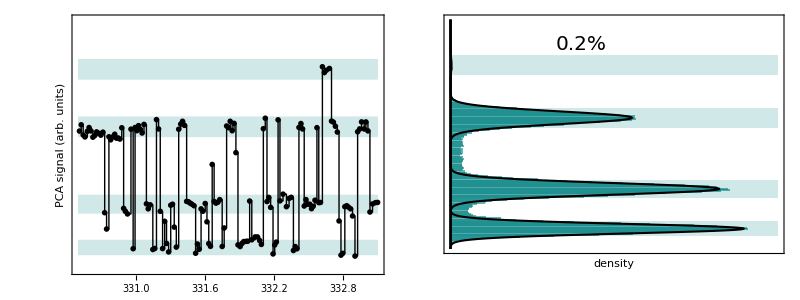
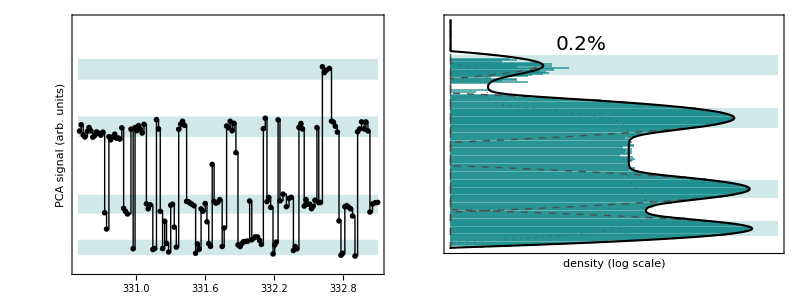

```mathematica
(* ---- occupation plot: a stretch of the PCA trace with the bands of the four levels (left), and the histogram of the
   whole record with the fitted levels (right), with a linear (occFigLin) and a logarithmic (occFigLog) density axis. The sign of a principal component is arbitrary; the trace is shown with
   the sign used for the assignment (st["sign"]), so that the levels 1 < 2 < 3 < 4 run from bottom to top. ---- *)
tWin = {330.5, 333.1};                      (* s; long dwells in 1, 2 and 3 and one visit to 4 *)
nSig = 1.5;                                 (* half-width of the shaded bands, in standard deviations of each level *)
yAll = st["display"]; 
lev = st["levels"];
 wid = st["widths"]; 
wts = st["weights"];
(* curves and bands: display fit with a Gaussian for each level and a mid-jump component between each pair of levels
   (emFitDetector in the Setup); the assignment levels lev, wid, wts set the plot range and the state-4 label *)
fitD = emFitDetector[yAll, lev, wid, wts, True, 300];
{levD, widD, wtsD} = Lookup[fitD, {"means", "widths", "weights"}];
Print["display fit (display units): means = ", levD, ",  widths = ", widD, ",  level weights = ", wtsD,
  ",  mid-jump weights ", fitD["pairs"], " = ", fitD["pairWeights"], ",  total mid-jump = ", Total[fitD["pairWeights"]]];
(* evidence for state 4: the same fit without the Gaussian at level 4 (jumps to and from level 4 still allowed) *)
fitNo4 = emFitDetector[yAll, lev, wid, wts, True, 300, {1, 2, 3}];
Print["log-likelihood of the display fit = ", fitD["logL"], ";  without the Gaussian at level 4 it is lower by ",
  fitD["logL"] - fitNo4["logL"]];
win = Select[Range[Length[tt]], tWin[[1]] <= tt[[#]] <= tWin[[2]] &];
yRange = {lev[[1]] - 4 wid[[1]], lev[[4]] + 4 wid[[4]]};
bandsT = Table[{Opacity[0.18], teal, Rectangle[{tWin[[1]], levD[[k]] - nSig widD[[k]]}, {tWin[[2]], levD[[k]] + nSig widD[[k]]}]}, {k, 4}];
occTrace = ListLinePlot[Transpose[{tt[[win]], yAll[[win]]}], InterpolationOrder -> 0,
   PlotStyle -> Directive[Black, AbsoluteThickness[1]], Mesh -> All, MeshStyle -> Directive[Black, AbsolutePointSize[4]],
   Prolog -> bandsT, Frame -> True, Axes -> False, PlotRange -> {tWin, yRange},
   FrameTicks -> {{None, Table[{levD[[k]], tex[cfg["charge"][[k]], 20]}, {k, 4}]}, {Automatic, None}},
   FrameLabel -> {{tnr["PCA signal (arb. units)"], None}, {tex["t\\ (\\mathrm{s})"], None}},
   BaseStyle -> baseStyle, AspectRatio ->Full, ImageSize -> {820, 300}, ImagePadding -> {{40, 70}, {65, 10}}];

binW = (yRange[[2]] - yRange[[1]])/200;
yIn = Select[yAll, yRange[[1]] <= # <= yRange[[2]] &];
{binsH, densH} = HistogramList[yIn, {yRange[[1]], yRange[[2]], binW}, "PDF"];
densH = densH Length[yIn]/Length[yAll];                (* density of the whole record *)
yGrid = Subdivide[yRange[[1]], yRange[[2]], 800];
gauss = Table[wtsD[[k]] PDF[NormalDistribution[levD[[k]], widD[[k]]], yGrid], {k, 4}];
mid = Sum[With[{a = fitD["pairs"][[j, 1]], b = fitD["pairs"][[j, 2]]},
    fitD["pairWeights"][[j]] boxPDF[yGrid, levD[[a]], levD[[b]], (widD[[a]] + widD[[b]])/2]], {j, Length[fitD["pairs"]]}];
total = Total[gauss] + mid;                            (* the full display fit *)
pctLabel[x_] := Text[Style[ToString[Round[100 wts[[4]], 0.01]] <> "%", 20, FontFamily -> "Times New Roman"], {x, lev[[4]] + 1.8 wid[[4]]}];

(* (i) linear density axis *)
xMaxH = 1.1 Max[densH];
bandsH = Table[{Opacity[0.18], teal, Rectangle[{0, levD[[k]] - nSig widD[[k]]}, {xMaxH, levD[[k]] + nSig widD[[k]]}]}, {k, 4}];
occHistLin = Show[
   Graphics[{bandsH, {Opacity[0.6], teal, EdgeForm[None],
      Table[Rectangle[{0, binsH[[i]]}, {densH[[i]], binsH[[i + 1]]}], {i, Length[densH]}]}}],
   (* linear panel: the Gaussian components of the display fit only; the log panel shows the full fit *)
   ListLinePlot[Table[Transpose[{gauss[[k]], yGrid}], {k, 4}], PlotStyle -> Directive[Black, AbsoluteThickness[1.5]]],
   Frame -> True, Axes -> False, FrameTicks -> None, PlotRange -> {{0, xMaxH}, yRange},
   FrameLabel -> {{None, None}, {tnr["density", 20], None}},
   Epilog -> pctLabel[0.4 xMaxH],
   AspectRatio -> Full, ImageSize -> {170, 300}, ImagePadding -> {{5, 10}, {65, 10}}];

(* (ii) logarithmic density axis: state 4 shows up as a small bump *)
lMin = Log10[10^-3.5 Max[densH]]; 
lMax = Log10[2 Max[densH]];
lg[x_] := Max[Log10[Max[x, 10^-300]], lMin];           (* log10 of a density, clipped at the left edge of the panel *)
bandsH = Table[{Opacity[0.18], teal, Rectangle[{lMin, levD[[k]] - nSig widD[[k]]}, {lMax, levD[[k]] + nSig widD[[k]]}]}, {k, 4}];
occHistLog = Show[
   Graphics[{bandsH, {Opacity[0.6], teal, EdgeForm[None],
      Table[If[densH[[i]] > 0, Rectangle[{lMin, binsH[[i]]}, {lg[densH[[i]]], binsH[[i + 1]]}], {}], {i, Length[densH]}]}}],
   ListLinePlot[Table[Transpose[{lg /@ gauss[[k]], yGrid}], {k, 4}], PlotStyle -> Directive[GrayLevel[0.3], Dashed, AbsoluteThickness[1]]],
   ListLinePlot[Transpose[{lg /@ mid, yGrid}], PlotStyle -> Directive[GrayLevel[0.3], Dotted, AbsoluteThickness[1]]],
   ListLinePlot[Transpose[{lg /@ total, yGrid}], PlotStyle -> Directive[Black, AbsoluteThickness[1.5]]],
   Frame -> True, Axes -> False, FrameTicks -> None, PlotRange -> {{lMin, lMax}, yRange},
   FrameLabel -> {{None, None}, {tnr["density (log scale)", 20], None}},
   Epilog -> pctLabel[lMin + 0.4 (lMax - lMin)],
   AspectRatio -> Full, ImageSize -> {170, 300}, ImagePadding -> {{5, 10}, {65, 10}}];

occFigLin = Grid[{{occTrace, occHistLin}}, Spacings -> 0];
occFigLog = Grid[{{occTrace, occHistLog}}, Spacings -> 0];
Column[{occFigLin, occFigLog}]
```

```mathematica
Export["occupation-5549-linear.pdf", occFigLin]
Export["occupation-5549-log.pdf", occFigLog]
```

occupation-5549-linear.pdf

occupation-5549-log.pdf

### Benchmarks

```mathematica
{Ncount, Tdw, Wnaive} = countJumps[traj, Ttot];
Print["jump counts N[[to, from]]:"]; Print[MatrixForm[Ncount]];
Print["dwell times (s) = ", Tdw, ",  occupations = ", Tdw/Total[Tdw]];
Print["naive W[[to, from]] (1/s):"]; Print[MatrixForm[Chop[Wnaive]]];
affNaive = affMax[Wnaive, cfg["obsCD"]];
sigmaNaive = EPR[Wnaive];
Print["naive benchmark: A_max(+1) for ", cfg["obsCD"], " = ", affNaive, ",  sigma = ", sigmaNaive, " /s"];
If[ListQ[cfg["bandEdge"]],
  affBand = rateBand[Wnaive, Ncount, Tdw, cfg["bandEdge"], affMax[#, cfg["obsCD"]] &];
  sigmaBand = rateBand[Wnaive, Ncount, Tdw, cfg["bandEdge"], EPR];
  Print["band from the count on edge ", cfg["bandEdge"], ":  A_max(+1) in ", affBand, ",  sigma in ", sigmaBand]];
(* if the rare reverse edge was never recorded, the naive W has a zero rate there: A_max(+1) is -Infinity and EPR drops the
   edge, so there is no naive point; panels (c), (d) then show only the band *)
naiveOK = ! (ListQ[cfg["bandEdge"]] && Ncount[[cfg["bandEdge"][[2]], cfg["bandEdge"][[1]]]] == 0);
(* contribution of each edge to the naive entropy production *)
piN = steadyState[Wnaive];
edgeSigma = Flatten[Table[With[{f = Wnaive[[b, a]] piN[[a]], r = Wnaive[[a, b]] piN[[b]]},
     {{a, b}, If[f > 0 && r > 0, (f - r) Log[f/r], Missing[]]}], {a, 4}, {b, a + 1, 4}], 1];
Print[Grid[Prepend[edgeSigma, {"edge", "contribution to sigma (1/s)"}], Frame -> All]];
Print["share of the naive sigma on the edges of the ring 1-2-3: ",
  Total[Cases[edgeSigma, {e_, v_?NumericQ} /; SubsetQ[{1, 2, 3}, e] :> v]]/sigmaNaive];
(* Table I of the Supplemental Material: the seven cycles of the four-state network, each in the orientation with
   positive affinity, and the outcome q of the observable cfg["obsCD"] along it *)
cycles7 = {{1, 3, 2, 1}, {1, 4, 2, 1}, {1, 4, 3, 1}, {2, 4, 3, 2}, {1, 2, 4, 3, 1}, {1, 3, 2, 4, 1}, {1, 4, 3, 2, 1}};
Print[Grid[Prepend[Table[With[{c = If[cycleAffinity[Wnaive, cc] >= 0, cc, Reverse[cc]]},
     {StringRiffle[ToString /@ c, " -> "], cycleAffinity[Wnaive, c],
      Total[nuOf[cfg["obsCD"]][[#[[2]], #[[1]]]] & /@ Partition[c, 2, 1]]}], {cc, cycles7}],
    {"cycle", "A_c", "q for " <> ToString[cfg["obsCD"]]}], Frame -> All]];
```

jump counts N[[to, from]]:

(0 | 5262 | 1987 | 21
3489 | 0 | 4413 | 51
3752 | 2619 | 0 | 54
29 | 72 | 25 | 0)

dwell times (s) = {626.309,767.836,516.413,4.91335},  occupations = {0.326974,0.40086,0.269601,0.00256508}

naive W[[to, from]] (1/s):

(0 | 6.85302 | 3.84769 | 4.27407
5.57073 | 0 | 8.54548 | 10.3799
5.99065 | 3.41088 | 0 | 10.9905
0.046303 | 0.09377 | 0.0484109 | 0)

naive benchmark: A_max(+1) for {1,3} = 1.56832,  sigma = 1.47152 /s

edge | contribution to sigma (1/s)
{1,2} | 0.380334
{1,3} | 0.585728
{1,4} | 0.00134807
{2,3} | 0.488674
{2,4} | 0.00378061
{3,4} | 0.0116593

share of the naive sigma on the edges of the ring 1-2-3: 0.988591

cycle | A_c | q for {1, 3}
1 -> 3 -> 2 -> 1 | 1.56832 | 1
1 -> 4 -> 2 -> 1 | 0.388829 | 0
1 -> 4 -> 3 -> 1 | 0.457219 | -1
2 -> 4 -> 3 -> 2 | 1.63671 | 0
1 -> 2 -> 4 -> 3 -> 1 | 0.0683896 | -1
1 -> 3 -> 2 -> 4 -> 1 | 1.17949 | 1
1 -> 4 -> 3 -> 2 -> 1 | 2.02554 | 0

### Excursions and estimators

```mathematica
qCD = qOf[traj, cfg["obsCD"]];
{nPlus, nMinus} = {Count[qCD, _?Positive], Count[qCD, _?Negative]};
Print["observable ", cfg["obsCD"], ":  excursions = ", Length[qCD], ",  n(+1), n(-1) = ", {nPlus, nMinus}, ",  binomial p = ", binomP[nPlus, nMinus]];
{lnLo, sigLo} = lowerLimits[qCD, Ttot];
Print["rigorous ", cl, " lower limits:  ln P(+1)/P(-1) >= ", lnLo, ",  sigma_exc >= ", sigLo, " /s"];
If[nPlus > 0 && nMinus > 0, SeedRandom[11]; Print["estimates with bootstrap ", cl, " intervals: ", estBoot[qCD, Ttot]]];
(* first f*T seconds of the record, for panels (c), (d); x = t/T *)
SeedRandom[11];
sweep = timeSweep[traj, cfg["obsCD"], cfg["display"], cfg["fracs"] Ttot];
affSweep = Cases[sweep, {t_, {v_, _}} :> {t/Ttot, v}];
sigSweep = Cases[sweep, {t_, {_, v_}} :> {t/Ttot, v}];
```

observable {1,3}:  excursions = 6424,  n(+1), n(-1) = {2254,490},  binomial p = 7.10043×10^-269

rigorous 0.95 lower limits:  ln P(+1)/P(-1) >= 1.44332,  sigma_exc >= 1.20773 /s

estimates with bootstrap 0.95 intervals: {1.530.100.10,1.410.160.17}

### Panels

observable | n(+1) | n(-1) | binomial p
1
2 | 486 | 2254 | 1.14101×10^-270
1
3 | 2254 | 490 | 7.10043×10^-269
2
3 | 486 | 2279 | 4.35633×10^-276
2
4 | 47 | 26 | 0.0186178
4
3 | 45 | 16 | 0.000264279

n(+1), n(-1) = {2254,490},  binomial p = 7.10043×10^-269,  KS distance = 0.0872227,  KS p (durations) = 0.00437813

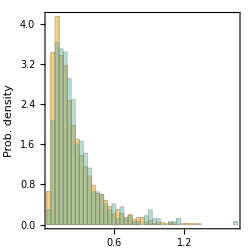

```mathematica
(* (a) duration distributions P(t|+1), P(t|-1) for cfg["obsB"] (here 1 -> 3); inset: number of excursions with q = +1
   (net 1 -> 3) and q = -1 (net 3 -> 1), Garwood bars. Both P(q) != P(-q) and P(t|q) != P(t|-q) violate detailed balance.
   The counts for every edge observable are printed first. *)
obsList = cfg["obsA"];
obsCounts = Table[With[{q = qOf[traj, e]}, {Count[q, _?Positive], Count[q, _?Negative]}], {e, obsList}];
Print[TableForm[Table[{obsList[[i]], obsCounts[[i, 1]], obsCounts[[i, 2]], binomP @@ obsCounts[[i]]}, {i, Length[obsList]}],
   TableHeadings -> {None, {"observable", "n(+1)", "n(-1)", "binomial p"}}]];

excA = excursionsOut[traj, aState, nuOf[cfg["obsB"]]];
tP = Pick[excA["duration"], excA["q"], 1]; tM = Pick[excA["duration"], excA["q"], -1];
{nP, nM} = {Length[tP], Length[tM]};
Print["n(+1), n(-1) = ", {nP, nM}, ",  binomial p = ", binomP[nP, nM],
  ",  KS distance = ", KolmogorovSmirnovTest[tP, tM, "TestStatistic"], ",  KS p (durations) = ", KolmogorovSmirnovTest[tP, tM, "PValue"]];

tCut = Quantile[Join[tP, tM], 0.99];                  (* x range of the histogram *)
binWt = 2 Mean[Differences[tt]];                      (* bin width = 2 samples: avoids aliasing with the sampling grid *)
legsH = SwatchLegend[{yellow, green}, tex[#, 17] & /@ {"P(t\\,|+1)", "P(t\\,|-1)"}, LegendMarkerSize -> 14, Spacings -> .001];
ciP = poissonCI[nP, cl]; ciM = poissonCI[nM, cl];
insetBars = Graphics[{
    {yellow, EdgeForm[None], Rectangle[{0.6, 0}, {1.4, nP}]},
    {green, EdgeForm[None], Rectangle[{1.6, 0}, {2.4, nM}]},
    {GrayLevel[0.25], Thickness[0.012], Line[{{1, ciP[[1]]}, {1, ciP[[2]]}}], Line[{{2, ciM[[1]]}, {2, ciM[[2]]}}]},
    Text[Style[nP, 11, FontFamily -> "Times New Roman"], {1, ciP[[2]] + 0.09 nP}],
    Text[Style[nM, 11, FontFamily -> "Times New Roman"], {2, ciM[[2]] + 0.09 nP}]},
   Frame -> True, AspectRatio -> 1, PlotRange -> {{0.3, 2.7}, {0, 1.25 nP}},
   FrameTicks -> {{None, None}, {{{1, tex["1\\to 3", 13]}, {2, tex["3\\to 1", 13]}}, None}},
   BaseStyle -> {FontSize -> 12, FontFamily -> "Times New Roman"}, ImageSize -> 150];
edgeplot = Histogram[{tP, tM}, {0, Max[Join[tP, tM]] + binWt, binWt}, "PDF",
   ChartLayout -> "Overlapped",
   ChartStyle -> {Directive[Opacity[0.6], yellow, EdgeForm[GrayLevel[0.5]]], Directive[Opacity[0.45], green, EdgeForm[GrayLevel[0.5]]]},
   Frame -> True, AspectRatio -> 1, ImageSize -> 250,
   PlotRange -> {{0.05, 1.75 tCut}, All},
   BaseStyle -> baseStyle,
   FrameLabel -> {tex["t\\ (\\mathrm{s})"], tnr["Prob. density"]},
   Epilog -> {Inset[insetBars, Scaled[{0.77, 0.72}], Center, Scaled[{0.48, 0.48}]], Inset[legsH, Scaled[{0.77, 0.25}]]}]
```

durations for {1,3}: n(+1) = 2254, n(-1) = 490,  KS p = 0.00437813

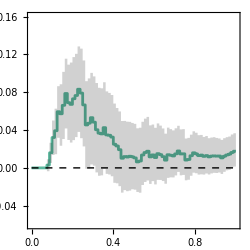

```mathematica
(* (b) F+(t) - F-(t) of the excursion durations for cfg["obsB"], bootstrap band; x = t/tmaxB (98% quantile of the durations) *)
excB = excursionsOut[traj, aState, nuOf[cfg["obsB"]]];
tauPlus = Pick[excB["duration"], excB["q"], 1];
tauMinus = Pick[excB["duration"], excB["q"], -1];
tmaxB = Quantile[Join[tauPlus, tauMinus], 0.98];
gridB = Subdivide[0., N@tmaxB, 80];
diffB = CDF[EmpiricalDistribution[tauPlus], gridB] - CDF[EmpiricalDistribution[tauMinus], gridB];
SeedRandom[3];
matB = Transpose@Table[
    CDF[EmpiricalDistribution[RandomChoice[tauPlus, Length[tauPlus]]], gridB] -
     CDF[EmpiricalDistribution[RandomChoice[tauMinus, Length[tauMinus]]], gridB], {1000}];
loB = Quantile[#, (1 - cl)/2] & /@ matB;
hiB = Quantile[#, 1 - (1 - cl)/2] & /@ matB;
Print["durations for ", cfg["obsB"], ": n(+1) = ", Length[tauPlus], ", n(-1) = ", Length[tauMinus], ",  KS p = ", KolmogorovSmirnovTest[tauPlus, tauMinus, "PValue"]];
diffplot = Show[
  ListLinePlot[staircase[gridB/tmaxB, diffB], PlotStyle -> green, ImageSize -> 250, AspectRatio -> 1,
   BaseStyle -> baseStyle,
   FrameLabel -> {tex["t/T_{\\max}"], tex["F_{+}(t)-F_{-}(t)"]},
   PlotRange -> {{0, 1.0}, {-0.06, 0.16}}],
  Graphics[{Opacity[0.18], Polygon[bandPolygon[gridB/tmaxB, loB, hiB]]}],
  Graphics[{Dashed, Line[{{0, 0}, {1, 0}}]}]]
```

```mathematica
(* (c) affinity: estimate with bootstrap bars against the naive W (dashed) *)
lx0 = 0.; lx1 = 1.05;   (* x axis = t/T, fraction of the record *)
affBot = 0.8; affTop = 2.8;
labelsA = tex[#, 17] & /@ {"\\ln P(1)/P(-1)", "\\mathcal{A}_{\\text{max}}(+1)"};
legsA = Column[{PointLegend[{green}, {labelsA[[1]]}, LegendMarkerSize -> 17, Spacings -> .001, LegendMarkers -> "●"],
    LineLegend[{Directive[blue, Dashed]}, {labelsA[[2]]}, LegendMarkerSize -> 17, Spacings -> .001]}, Spacings -> -0.7];
affplot = Show[
  ListPlot[affSweep, PlotMarkers -> {Graphics[{green, Disk[]}], 0.05}, IntervalMarkersStyle -> {Directive[green]},
   BaseStyle -> baseStyle,
   FrameLabel -> {tex["t/T_{\\textrm{tot}}"], None},
   AspectRatio -> 1, ImageSize -> 250, PlotRange -> {{lx0, lx1}, {1.4 affBot, 0.75 affTop}},
   Epilog -> Inset[legsA, Scaled[{.70, .88}]]],
  Graphics[{blue, Dashed, Thickness[0.01], Line[{{lx0, affNaive}, {lx1, affNaive}}]}]]
```

-Graphics-

```mathematica
(* (d) entropy production: estimate with bootstrap bars against the naive W (dashed) *)
lx0 = 0.; lx1 = 1.05;
sigBot = 0.4; sigTop = 3.0;
labelsS = tex[#, 17] & /@ {"\\hat{\\sigma}_{\\text{exc}}", "\\sigma_{\\Delta t}"};
legsS = Column[{PointLegend[{green}, {labelsS[[1]]}, LegendMarkerSize -> 17, Spacings -> .001, LegendMarkers -> "●"],
    LineLegend[{Directive[yellow, Dashed]}, {labelsS[[2]]}, LegendMarkerSize -> 17, Spacings -> .001]}, Spacings -> -0.7];
sigplot = Show[
  ListPlot[sigSweep, PlotMarkers -> {Graphics[{green, Disk[]}], 0.05}, IntervalMarkersStyle -> {Directive[green]},
   BaseStyle -> baseStyle,
   FrameLabel -> {tex["t/T_{\\textrm{tot}}"], None},
   AspectRatio -> 1, ImageSize -> 250, PlotRange -> {{lx0, lx1}, {1.8 sigBot, 0.7 sigTop}},
   Epilog -> Inset[legsS, Scaled[{.7, .88}]]],
  Graphics[{yellow, Dashed, Thickness[0.01], Line[{{lx0, sigmaNaive}, {lx1, sigmaNaive}}]}]]
```

-Graphics-

```mathematica
fig = If[DownValues[grid] =!= {},
   grid[{edgeplot, diffplot, affplot, sigplot}, 1, {0.14, 0.92}, 22],
   GraphicsRow[{edgeplot, diffplot, affplot, sigplot}, ImageSize -> 1100]];
figs[cfg["id"]] = fig;
results[cfg["id"]] = <|"cfg" -> cfg, "traj" -> traj, "Ttot" -> Ttot, "W" -> Wnaive, "lnLo" -> lnLo, "sigLo" -> sigLo, "sweep" -> sweep|>;
fig
```

-Graphics-

```mathematica
Export[cfg["export"], fig]
```

results-5549.pdf

### Statistics quoted in the text

Numbers quoted in the text: p-values of panels (a), (b), detection time, directedness of the visits to state 4, the excursion statistics predicted by the naive W, and the significance of the gap between estimators and benchmark.

```mathematica
(* ---- (1) p-values of panels (a) and (b), observable cfg["obsB"] ----
   (a) frequencies: exact two-sided binomial test of P(+1) = P(-1) given n = n(+1) + n(-1).
   (b) durations:   two-sample Kolmogorov-Smirnov test of P(t|+1) = P(t|-1), plus a permutation p-value
                    (2 x 10^4 shuffles of the labels +1/-1 among the nonzero excursions), which makes no assumption on ties. *)
excS = excursionsOut[traj, aState, nuOf[cfg["obsB"]]];
tPs = Pick[excS["duration"], excS["q"], 1]; tMs = Pick[excS["duration"], excS["q"], -1];
(* exact two-sample KS distance, computed on the union of the observed values; fast enough for 2 x 10^4 shuffles *)
ksD[x_, y_] := Module[{e = Append[#, Last[#] + 1] &[Union[Join[x, y]]]},
   N@Max[Abs[Accumulate[BinCounts[x, {e}]]/Length[x] - Accumulate[BinCounts[y, {e}]]/Length[y]]]];
dObs = ksD[tPs, tMs];
SeedRandom[5];
permD = Module[{all = Join[tPs, tMs], np = Length[tPs], sh}, Table[sh = RandomSample[all]; ksD[sh[[;; np]], sh[[np + 1 ;;]]], {20000}]];
Print[Grid[{
    {"observable", "n(+1)", "n(-1)", "binomial p", "KS distance D", "KS p", "permutation p (20000 shuffles)"},
    {cfg["obsB"], Length[tPs], Length[tMs], binomP[Length[tPs], Length[tMs]], dObs,
     KolmogorovSmirnovTest[tPs, tMs, "PValue"], N[(1 + Count[permD, d_ /; d >= dObs])/(1 + Length[permD])]}}, Frame -> All]];
```

observable | n(+1) | n(-1) | binomial p | KS distance D | KS p | permutation p (20000 shuffles)
{1,3} | 2254 | 490 | 7.10043×10^-269 | 0.0872227 | 0.00437813 | 0.00454977

```mathematica
(* ---- (2) how much data is needed to detect the violation, observable cfg["obsCD"] ----
   Excursions are ordered by their start time; for the first tm seconds of the record both tests are recomputed.
   tDetect = first time at which the binomial p-value drops below 10^-3 (and 10^-5). *)
excT = excursionsOut[traj, aState, nuOf[cfg["obsCD"]]];
qT = excT["q"]; durT = excT["duration"];
startT = traj[[excT["start"], 1]];                       (* start time of every excursion *)
detTable = Table[With[{m = Pick[Range[Length[qT]], Thread[startT <= tm]]},
    With[{qq = qT[[m]], dd = durT[[m]]},
     With[{a = Count[qq, 1], b = Count[qq, -1]},
      {tm, a, b, binomP[a, b],
       If[Min[a, b] >= 5, KolmogorovSmirnovTest[Pick[dd, qq, 1], Pick[dd, qq, -1], "PValue"], "-"]}]]],
   {tm, {5, 10, 20, 50, 100, 200, 500, 1000, Ttot}}];
Print[Grid[Prepend[detTable, {"first t (s)", "n(+1)", "n(-1)", "binomial p", "KS p"}], Frame -> All]];
(* exact detection time: scan the nonzero excursions in time order *)
nz = Pick[Range[Length[qT]], Unitize[qT], 1];
cumP = Accumulate[Boole[Positive /@ qT[[nz]]]];          (* running n(+1) *)
cumN = Range[Length[nz]] - cumP;                         (* running n(-1) *)
pRun = MapThread[binomP, {cumP, cumN}];
tDetect[lev_] := With[{k = FirstPosition[pRun, x_ /; x < lev, {Missing[]}][[1]]},
   If[MissingQ[k], {Missing["never"], Missing["never"]}, {startT[[nz[[k]]]], k}]];
Print["binomial p < 10^-3 first reached at t = ", tDetect[10^-3][[1]], " s, after ", tDetect[10^-3][[2]], " nonzero excursions"];
Print["binomial p < 10^-5 first reached at t = ", tDetect[10^-5][[1]], " s, after ", tDetect[10^-5][[2]], " nonzero excursions"];
```

first t (s) | n(+1) | n(-1) | binomial p | KS p
5 | 7 | 1 | 0.0703125 | -
10 | 13 | 2 | 0.00738525 | -
20 | 25 | 3 | 0.0000274405 | -
50 | 64 | 11 | 3.10852×10^-10 | 0.47352
100 | 115 | 22 | 2.15378×10^-16 | 0.221058
200 | 211 | 47 | 5.45339×10^-26 | 0.105893
500 | 555 | 127 | 1.20101×10^-64 | 0.0412758
1000 | 1142 | 247 | 1.21745×10^-137 | 0.00198899
1915.49 | 2254 | 490 | 7.10043×10^-269 | 0.00437813

binomial p < 10^-3 first reached at t = 12.5196 s, after 19 nonzero excursions

binomial p < 10^-5 first reached at t = 21.0894 s, after 30 nonzero excursions

```mathematica
(* ---- (3) excursions through state 4 are directed ----
   Same test for observables on the edges of state 4. A time-symmetric artifact (noise, misassigned samples) produces
   equal counts in both directions, so a significant asymmetry means a directed, dissipative channel. *)
obs4 = {{2, 4}, {4, 3}, {1, 4}};
Print[Grid[Prepend[Table[With[{q = qOf[traj, e]}, With[{a = Count[q, _?Positive], b = Count[q, _?Negative]},
       {ToString[e[[1]]] <> " -> " <> ToString[e[[2]]], a, b, binomP[a, b]}]], {e, obs4}],
    {"observable (+1 for)", "n(+1)", "n(-1)", "binomial p"}], Frame -> All]];
Print["visits to state 4: ", Count[traj[[All, 2]], 4], ",  occupancy of state 4 (naive) = ", Tdw[[4]]/Total[Tdw]];
```

observable (+1 for) | n(+1) | n(-1) | binomial p
2 -> 4 | 47 | 26 | 0.0186178
4 -> 3 | 45 | 16 | 0.000264279
1 -> 4 | 23 | 16 | 0.336784

visits to state 4: 126,  occupancy of state 4 (naive) = 0.00256508

```mathematica
(* ---- (4) excursion statistics predicted by the naive rate matrix, against the measured ones ----
   The triangle-only row (states 1, 2, 3, same rates) is shown when the observable does not touch state 4. *)
pred = predictExcursions[Wnaive, aState, nuOf[cfg["obsCD"]]];
lnMeas = If[nPlus > 0 && nMinus > 0, Log[N[nPlus/nMinus]], "-"];
sigMeas = If[nPlus > 0 && nMinus > 0, ((nPlus - nMinus)/Ttot) Log[N[nPlus/nMinus]], "-"];
W3 = Wnaive[[1 ;; 3, 1 ;; 3]];
Print[Grid[DeleteCases[{
    {"", "A_max(+1)", "ln P(+1)/P(-1)", "sigma (1/s)", "sigma_exc (1/s)"},
    {"naive W, 4 states (prediction)", affNaive, pred["lnRatio"], sigmaNaive, pred["sigmaExc"]},
    If[FreeQ[cfg["obsCD"], 4],
     With[{p3 = predictExcursions[W3, aState, nuOf[cfg["obsCD"], 3]]},
      {"triangle 1-2-3 only (prediction)", affMax[W3, cfg["obsCD"]], p3["lnRatio"], EPR[W3], p3["sigmaExc"]}], Nothing],
    {"measured excursions", "", lnMeas, "", sigMeas}}, Nothing], Frame -> All]];
Print["check: excursion rate predicted from W = ", pred["K"], " /s,  measured = ", Length[qCD]/Ttot, " /s"];
```

| A_max(+1) | ln P(+1)/P(-1) | sigma (1/s) | sigma_exc (1/s)
naive W, 4 states (prediction) | 1.56832 | 1.54867 | 1.47152 | 1.42701
triangle 1-2-3 only (prediction) | 1.56832 | 1.56832 | 1.45778 | 1.45778
measured excursions |  | 1.52606 |  | 1.40536

check: excursion rate predicted from W = 3.35426 /s,  measured = 3.35371 /s

```mathematica
(* ---- (5) is the gap between the excursion estimators and the naive W significant? paired bootstrap ----
   Resample whole units (a visit to A plus the excursion that follows), recompute the naive W AND the excursion estimators
   from the same resample, and record the gaps; this keeps the correlation between the two sides. Needs enough reverse
   excursions, otherwise it is skipped. *)
If[nMinus >= 10, (
  iA = Flatten[Position[traj[[All, 2]], aState]];
  dV = Differences[Append[traj[[All, 1]], Ttot]];
  nuCD = nuOf[cfg["obsCD"]];
  unitStats = Table[Module[{a = iA[[k]], b = iA[[k + 1]], Nc = ConstantArray[0, {4, 4}], Td = ConstantArray[0., 4]},
     Do[Td[[traj[[j, 2]]]] += dV[[j]]; Nc[[traj[[j + 1, 2]], traj[[j, 2]]]] += 1, {j, a, b - 1}];
     {Nc, Td, Total[nuCD[[#[[2]], #[[1]]]] & /@ Partition[traj[[a ;; b, 2]], 2, 1]]}],
    {k, Length[iA] - 1}];
  gapStats[us_] := Module[{Nc = Total[us[[All, 1]]], Td = Total[us[[All, 2]]], q = us[[All, 3]], W, T, a, b, lr, sx},
    W = N[Nc/ConstantArray[Td, 4]]; T = Total[Td];
    a = Count[q, _?Positive]; b = Count[q, _?Negative]; lr = Log[a/b]; sx = ((a - b)/T) lr;
    {affMax[W, cfg["obsCD"]] - lr, EPR[W] - sx, lr/affMax[W, cfg["obsCD"]], sx/EPR[W]}];
  gap0 = gapStats[unitStats];
  SeedRandom[9];
  gapBoot = Table[gapStats[RandomChoice[unitStats, Length[unitStats]]], {300}];
  Print[Grid[{
     {"", "estimate", "95% interval", "fraction of resamples with gap <= 0"},
     {"A_naive - ln P(+1)/P(-1)", gap0[[1]], Quantile[gapBoot[[All, 1]], {0.025, 0.975}], N@Count[gapBoot[[All, 1]], x_ /; x <= 0]/300},
     {"sigma_naive - sigma_exc", gap0[[2]], Quantile[gapBoot[[All, 2]], {0.025, 0.975}], N@Count[gapBoot[[All, 2]], x_ /; x <= 0]/300},
     {"recovered fraction, affinity", gap0[[3]], Quantile[gapBoot[[All, 3]], {0.025, 0.975}], ""},
     {"recovered fraction, sigma", gap0[[4]], Quantile[gapBoot[[All, 4]], {0.025, 0.975}], ""}}, Frame -> All]]
  ), Print["(5) skipped: n(-1) = ", nMinus, " is too small for the paired bootstrap"]];
```

| estimate | 95% interval | fraction of resamples with gap <= 0
A_naive - ln P(+1)/P(-1) | 0.0415817 | {-0.00739917,0.279099} | 0.0433333
sigma_naive - sigma_exc | 0.0647034 | {0.0161729,0.125968} | 0.01
recovered fraction, affinity | 0.973475 | {0.846255,1.00483} | 
recovered fraction, sigma | 0.955993 | {0.915728,0.988785} |

## Negative bias: -0.955 V / 6013

Negative bias -0.955 V / 6013 (Supplemental Material). The triangle 1-2-3 is balanced and state 4 is visited one way, 2 -> 4 -> 3. Panels: (a) every edge observable, (b) durations for 1 -> 3 (control), (c), (d) the observable 4 -> 3, a boundary observable of A = {3}, with rigorous lower limits against the naive W (line) and its Poisson band from the recorded 3 -> 4 jumps (shaded).

### Configuration

```mathematica
cfg = <|
   "id" -> "6013",
   "dir" -> FileNameJoin[{dataRoot, "-0.955 bias", "6013"}],
   "charge" -> {"(00)", "(10)", "(01)", "(02)"},          (* states 1, 2, 3, 4 at negative bias *)
   "rMax" -> 4, "minVisit" -> 2, "xFar" -> 4.5,          (* state assignment *)
   "obsA" -> {{1, 2}, {1, 3}, {2, 3}, {2, 4}, {4, 3}},   (* panel (a) *)
   "obsB" -> {1, 3},                                     (* panel (b): right-barrier tunneling, control *)
   "obsCD" -> {4, 3},                                    (* panels (c), (d): boundary observable of A = {3} *)
   "display" -> "lowerLimit",                            (* reverse excursions are rare: rigorous lower limits *)
   "fracs" -> Range[0.1, 1, 0.1],                        (* fractions t/T of the record for panels (c), (d) *)
   "bandEdge" -> {3, 4},                                 (* rare reverse edge 3 -> 4 sets the benchmark band *)
   "export" -> "results-6013.pdf"|>;
```

```mathematica
run = loadRun[cfg["dir"]];
tt = run["t"]; Ttot = Last[tt];
st = assignStatesPCA[run, cfg];
traj = st["traj"];
If[TrueQ[useSingleModel],
  With[{alt = assignFromFit[st["display"], tt, displayFitOf[st, cfg["id"]], cfg["minVisit"]]},
   traj = alt["traj"];
   Print["single model: states assigned from the display fit,  transit fraction = ", alt["transit"], ",  visits = ", Length[traj]]]];
```

samples = 111331,  duration = 1879.23 s,  mean dt = 0.0168798 s

PCA sign = -1,  levels of states 1, 2, 3 = {-1.41091,0.195739,5.18575},  widths = {0.366596,0.406178,1.01663}  (standardised units)

candidates for state 4 = 69,  level of state 4 = 12.7938

transit fraction = 0.0000269467,  occupancy 1, 2, 3, 4 = {0.326944,0.56341,0.108945,0.000673667}

number of visits = 12637

General::munfl: 0.294258 1.016434715323×10^-337 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.294258 3.338292475826×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.294258 8.227268888644×10^-329 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

single model: states assigned from the display fit,  transit fraction = 0.,  visits = 12644

### Occupation plot

General::munfl: 0.294258 1.016434715323×10^-337 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.294258 3.338292475826×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.294258 8.227268888644×10^-329 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

display fit (display units): means = {-0.00404937,-0.000057052,0.0122781,0.0309974},  widths = {0.000897016,0.000982548,0.00147934,0.00147934},  level weights = {0.313846,0.555609,0.103783,0.000512801},  mid-jump weights {{1,2},{1,3},{2,3},{1,4},{2,4},{3,4}} = {0.0178272,0.00486891,0.00296006,0.000246633,0.000147646,0.000190167},  total mid-jump = 0.0262406

General::munfl: 0.294456 1.016434715323×10^-337 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.294456 3.338292475826×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.294456 8.227268888644×10^-329 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

log-likelihood of the display fit = 508537.;  without the Gaussian at level 4 it is lower by 369.733

General::munfl: 0.313846 5.792714046804×10^-309 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.313846 4.439133027119×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.313846 3.386228225894×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

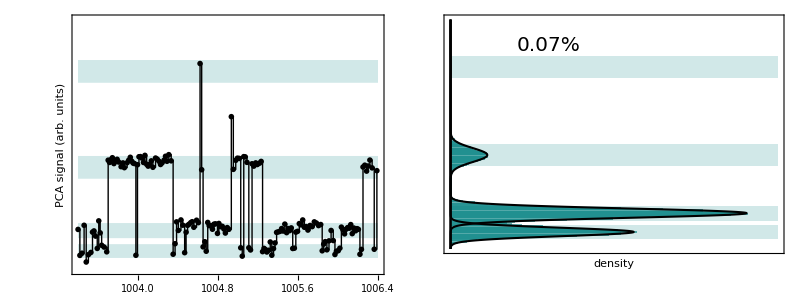
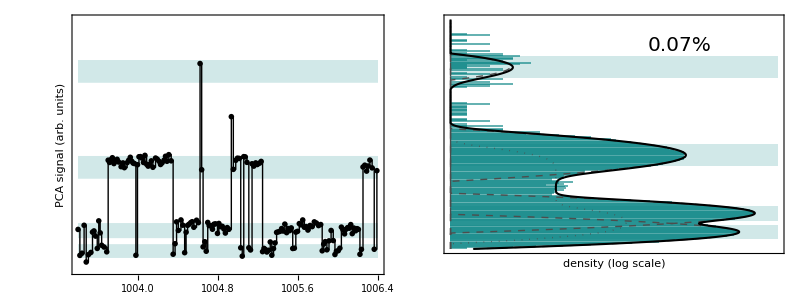

```mathematica
(* ---- occupation plot at negative bias, state 4 = (02): a stretch of the PCA trace with the bands of the four levels (left), and the histogram of the
   whole record with the fitted levels (right), with a linear (occFigLin) and a logarithmic (occFigLog) density axis. The sign of a principal component is arbitrary; the trace is shown with
   the sign used for the assignment (st["sign"]), so that the levels 1 < 2 < 3 < 4 run from bottom to top. ---- *)
tWin = {1003.4, 1006.4};                    (* s; dwells in 1, 2 and 3 and two passages 2 -> 4 -> 3, the one-way loop *)
nSig = 1.5;                                 (* half-width of the shaded bands, in standard deviations of each level *)
yAll = st["display"]; lev = st["levels"]; wid = st["widths"]; wts = st["weights"];
(* curves and bands: display fit with a Gaussian for each level and a mid-jump component between each pair of levels
   (emFitDetector in the Setup); the assignment levels lev, wid, wts set the plot range and the state-4 label *)
fitD = emFitDetector[yAll, lev, wid, wts, True, 300];
{levD, widD, wtsD} = Lookup[fitD, {"means", "widths", "weights"}];
Print["display fit (display units): means = ", levD, ",  widths = ", widD, ",  level weights = ", wtsD,
  ",  mid-jump weights ", fitD["pairs"], " = ", fitD["pairWeights"], ",  total mid-jump = ", Total[fitD["pairWeights"]]];
(* evidence for state 4: the same fit without the Gaussian at level 4 (jumps to and from level 4 still allowed) *)
fitNo4 = emFitDetector[yAll, lev, wid, wts, True, 300, {1, 2, 3}];
Print["log-likelihood of the display fit = ", fitD["logL"], ";  without the Gaussian at level 4 it is lower by ",
  fitD["logL"] - fitNo4["logL"]];
win = Select[Range[Length[tt]], tWin[[1]] <= tt[[#]] <= tWin[[2]] &];
yRange = {lev[[1]] - 4 wid[[1]], lev[[4]] + 4 wid[[4]]};
bandsT = Table[{Opacity[0.18], teal, Rectangle[{tWin[[1]], levD[[k]] - nSig widD[[k]]}, {tWin[[2]], levD[[k]] + nSig widD[[k]]}]}, {k, 4}];
occTrace = ListLinePlot[Transpose[{tt[[win]], yAll[[win]]}], InterpolationOrder -> 0,
   PlotStyle -> Directive[Black, AbsoluteThickness[1]], Mesh -> All, MeshStyle -> Directive[Black, AbsolutePointSize[4]],
   Prolog -> bandsT, Frame -> True, Axes -> False, PlotRange -> {tWin, yRange},
   FrameTicks -> {{None, Table[{levD[[k]], tex[cfg["charge"][[k]], 20]}, {k, 4}]}, {Automatic, None}},
   FrameLabel -> {{tnr["PCA signal (arb. units)"], None}, {tex["t\\ (\\mathrm{s})"], None}},
   BaseStyle -> baseStyle, AspectRatio -> Full, ImageSize -> {820, 300}, ImagePadding -> {{40, 70}, {65, 10}}];

binW = (yRange[[2]] - yRange[[1]])/200;
yIn = Select[yAll, yRange[[1]] <= # <= yRange[[2]] &];
{binsH, densH} = HistogramList[yIn, {yRange[[1]], yRange[[2]], binW}, "PDF"];
densH = densH Length[yIn]/Length[yAll];                (* density of the whole record *)
yGrid = Subdivide[yRange[[1]], yRange[[2]], 800];
gauss = Table[wtsD[[k]] PDF[NormalDistribution[levD[[k]], widD[[k]]], yGrid], {k, 4}];
mid = Sum[With[{a = fitD["pairs"][[j, 1]], b = fitD["pairs"][[j, 2]]},
    fitD["pairWeights"][[j]] boxPDF[yGrid, levD[[a]], levD[[b]], (widD[[a]] + widD[[b]])/2]], {j, Length[fitD["pairs"]]}];
total = Total[gauss] + mid;                            (* the full display fit *)
pctLabel[x_] := Text[Style[ToString[Round[100 wts[[4]], 0.01]] <> "%", 20, FontFamily -> "Times New Roman"], {x, lev[[4]] + 1.8 wid[[4]]}];

(* (i) linear density axis *)
xMaxH = 1.1 Max[densH];
bandsH = Table[{Opacity[0.18], teal, Rectangle[{0, levD[[k]] - nSig widD[[k]]}, {xMaxH, levD[[k]] + nSig widD[[k]]}]}, {k, 4}];
occHistLin = Show[
   Graphics[{bandsH, {Opacity[0.6], teal, EdgeForm[None],
      Table[Rectangle[{0, binsH[[i]]}, {densH[[i]], binsH[[i + 1]]}], {i, Length[densH]}]}}],
   (* linear panel: the Gaussian components of the display fit only (caption: "Gaussian components of a fit that
      also accounts for the samples recorded during jumps"); the log panel shows the full fit *)
   ListLinePlot[Table[Transpose[{gauss[[k]], yGrid}], {k, 4}], PlotStyle -> Directive[Black, AbsoluteThickness[1.5]]],
   Frame -> True, Axes -> False, FrameTicks -> None, PlotRange -> {{0, xMaxH}, yRange},
   FrameLabel -> {{None, None}, {tnr["density", 20], None}},
   Epilog -> pctLabel[0.3 xMaxH],
   AspectRatio -> Full, ImageSize -> {170, 300}, ImagePadding -> {{5, 10}, {65, 10}}];

(* (ii) logarithmic density axis: state 4 shows up as a small bump *)
lMin = Log10[10^-4 Max[densH]]; lMax = Log10[2 Max[densH]];
lg[x_] := Max[Log10[Max[x, 10^-300]], lMin];           (* log10 of a density, clipped at the left edge of the panel *)
bandsH = Table[{Opacity[0.18], teal, Rectangle[{lMin, levD[[k]] - nSig widD[[k]]}, {lMax, levD[[k]] + nSig widD[[k]]}]}, {k, 4}];
occHistLog = Show[
   Graphics[{bandsH, {Opacity[0.6], teal, EdgeForm[None],
      Table[If[densH[[i]] > 0, Rectangle[{lMin, binsH[[i]]}, {lg[densH[[i]]], binsH[[i + 1]]}], {}], {i, Length[densH]}]}}],
   ListLinePlot[Table[Transpose[{lg /@ gauss[[k]], yGrid}], {k, 4}], PlotStyle -> Directive[GrayLevel[0.3], Dashed, AbsoluteThickness[1]]],
   ListLinePlot[Transpose[{lg /@ mid, yGrid}], PlotStyle -> Directive[GrayLevel[0.3], Dotted, AbsoluteThickness[1]]],
   ListLinePlot[Transpose[{lg /@ total, yGrid}], PlotStyle -> Directive[Black, AbsoluteThickness[1.5]]],
   Frame -> True, Axes -> False, FrameTicks -> None, PlotRange -> {{lMin, lMax}, yRange},
   FrameLabel -> {{None, None}, {tnr["density (log scale)", 20], None}},
   Epilog -> pctLabel[lMin + 0.7 (lMax - lMin)],
   AspectRatio -> Full, ImageSize -> {170, 300}, ImagePadding -> {{5, 10}, {65, 10}}];

occFigLin = Grid[{{occTrace, occHistLin}}, Spacings -> 0];
occFigLog = Grid[{{occTrace, occHistLog}}, Spacings -> 0];
Column[{occFigLin, occFigLog}]
```

```mathematica
Export["occupation-6013-linear.pdf", occFigLin]
Export["occupation-6013-log.pdf", occFigLog]
```

occupation-6013-linear.pdf

occupation-6013-log.pdf

### Benchmarks

```mathematica
{Ncount, Tdw, Wnaive} = countJumps[traj, Ttot];
Print["jump counts N[[to, from]]:"]; Print[MatrixForm[Ncount]];
Print["dwell times (s) = ", Tdw, ",  occupations = ", Tdw/Total[Tdw]];
Print["naive W[[to, from]] (1/s):"]; Print[MatrixForm[Chop[Wnaive]]];
affNaive = affMax[Wnaive, cfg["obsCD"]];
sigmaNaive = EPR[Wnaive];
Print["naive benchmark: A_max(+1) for ", cfg["obsCD"], " = ", affNaive, ",  sigma = ", sigmaNaive, " /s"];
If[ListQ[cfg["bandEdge"]],
  affBand = rateBand[Wnaive, Ncount, Tdw, cfg["bandEdge"], affMax[#, cfg["obsCD"]] &];
  sigmaBand = rateBand[Wnaive, Ncount, Tdw, cfg["bandEdge"], EPR];
  Print["band from the count on edge ", cfg["bandEdge"], ":  A_max(+1) in ", affBand, ",  sigma in ", sigmaBand]];
(* if the rare reverse edge was never recorded, the naive W has a zero rate there: A_max(+1) is -Infinity and EPR drops the
   edge, so there is no naive point; panels (c), (d) then show only the band *)
naiveOK = ! (ListQ[cfg["bandEdge"]] && Ncount[[cfg["bandEdge"][[2]], cfg["bandEdge"][[1]]]] == 0);
(* contribution of each edge to the naive entropy production *)
piN = steadyState[Wnaive];
edgeSigma = Flatten[Table[With[{f = Wnaive[[b, a]] piN[[a]], r = Wnaive[[a, b]] piN[[b]]},
     {{a, b}, If[f > 0 && r > 0, (f - r) Log[f/r], Missing[]]}], {a, 4}, {b, a + 1, 4}], 1];
Print[Grid[Prepend[edgeSigma, {"edge", "contribution to sigma (1/s)"}], Frame -> All]];
Print["share of the naive sigma on the edges of the ring 1-2-3: ",
  Total[Cases[edgeSigma, {e_, v_?NumericQ} /; SubsetQ[{1, 2, 3}, e] :> v]]/sigmaNaive];
(* Table I of the Supplemental Material: the seven cycles of the four-state network, each in the orientation with
   positive affinity, and the outcome q of the observable cfg["obsCD"] along it *)
cycles7 = {{1, 3, 2, 1}, {1, 4, 2, 1}, {1, 4, 3, 1}, {2, 4, 3, 2}, {1, 2, 4, 3, 1}, {1, 3, 2, 4, 1}, {1, 4, 3, 2, 1}};
Print[Grid[Prepend[Table[With[{c = If[cycleAffinity[Wnaive, cc] >= 0, cc, Reverse[cc]]},
     {StringRiffle[ToString /@ c, " -> "], cycleAffinity[Wnaive, c],
      Total[nuOf[cfg["obsCD"]][[#[[2]], #[[1]]]] & /@ Partition[c, 2, 1]]}], {cc, cycles7}],
    {"cycle", "A_c", "q for " <> ToString[cfg["obsCD"]]}], Frame -> All]];
```

jump counts N[[to, from]]:

(0 | 4769 | 1057 | 6
4805 | 0 | 444 | 10
1019 | 451 | 0 | 33
8 | 40 | 1 | 0)

dwell times (s) = {598.131,1071.13,208.603,1.36367},  occupations = {0.318286,0.569984,0.111005,0.000725658}

naive W[[to, from]] (1/s):

(0 | 4.45231 | 5.06704 | 4.39988
8.03335 | 0 | 2.12844 | 7.33313
1.70364 | 0.421051 | 0 | 24.1993
0.013375 | 0.0373438 | 0.0047938 | 0)

naive benchmark: A_max(+1) for {4,3} = 4.92694,  sigma = 0.0829221 /s

band from the count on edge {3,4}:  A_max(+1) in {3.20925,8.60318},  sigma in {0.0514764,0.146898}

edge | contribution to sigma (1/s)
{1,2} | 0.000149386
{1,3} | 0.00076597
{1,4} | 0.000306372
{2,3} | 0.0000527585
{2,4} | 0.0221271
{3,4} | 0.0595205

share of the naive sigma on the edges of the ring 1-2-3: 0.011675

cycle | A_c | q for {4, 3}
1 -> 2 -> 3 -> 1 | 0.0597761 | 0
1 -> 2 -> 4 -> 1 | 1.10613 | 0
1 -> 4 -> 3 -> 1 | 3.8208 | 1
2 -> 4 -> 3 -> 2 | 4.86716 | 1
1 -> 2 -> 4 -> 3 -> 1 | 4.92694 | 1
1 -> 3 -> 2 -> 4 -> 1 | 1.04636 | 0
1 -> 4 -> 3 -> 2 -> 1 | 3.76103 | 1

### Excursions and estimators

```mathematica
qCD = qOf[traj, cfg["obsCD"]];
{nPlus, nMinus} = {Count[qCD, _?Positive], Count[qCD, _?Negative]};
Print["observable ", cfg["obsCD"], ":  excursions = ", Length[qCD], ",  n(+1), n(-1) = ", {nPlus, nMinus}, ",  binomial p = ", binomP[nPlus, nMinus]];
{lnLo, sigLo} = lowerLimits[qCD, Ttot];
Print["rigorous ", cl, " lower limits:  ln P(+1)/P(-1) >= ", lnLo, ",  sigma_exc >= ", sigLo, " /s"];
If[nPlus > 0 && nMinus > 0, SeedRandom[11]; Print["estimates with bootstrap ", cl, " intervals: ", estBoot[qCD, Ttot]]];
(* first f*T seconds of the record, for panels (c), (d); x = t/T *)
SeedRandom[11];
sweep = timeSweep[traj, cfg["obsCD"], cfg["display"], cfg["fracs"] Ttot];
affSweep = Cases[sweep, {t_, {v_, _}} :> {t/Ttot, v}];
sigSweep = Cases[sweep, {t_, {_, v_}} :> {t/Ttot, v}];
```

observable {4,3}:  excursions = 1502,  n(+1), n(-1) = {33,1},  binomial p = 4.07454×10^-9

rigorous 0.95 lower limits:  ln P(+1)/P(-1) >= 1.88275,  sigma_exc >= 0.014851 /s

estimates with bootstrap 0.95 intervals: {3.501.40.26,0.0600.0340.025}

### Panels

observable | n(+1) | n(-1) | binomial p
1
2 | 320 | 284 | 0.15435
1
3 | 284 | 323 | 0.122912
2
3 | 299 | 292 | 0.805083
2
4 | 30 | 1 | 2.98023×10^-8
4
3 | 33 | 1 | 4.07454×10^-9

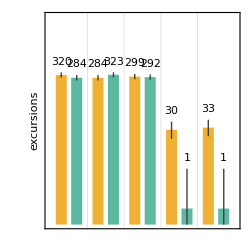

```mathematica
(* (a) excursions with q = +1 and q = -1 for each edge observable, A = {3}, Garwood error bars *)
obsList = cfg["obsA"];
obsCounts = Table[With[{q = qOf[traj, e]}, {Count[q, _?Positive], Count[q, _?Negative]}], {e, obsList}];
Print[TableForm[Table[{obsList[[i]], obsCounts[[i, 1]], obsCounts[[i, 2]], binomP @@ obsCounts[[i]]}, {i, Length[obsList]}],
   TableHeadings -> {None, {"observable", "n(+1)", "n(-1)", "binomial p"}}]];

y0 = Log10[0.5]; yTop = 3.6; wBar = 0.30; dx = 0.21;
barR[x_, n_, col_] := If[n > 0, {col, EdgeForm[None], Rectangle[{x - wBar/2, y0}, {x + wBar/2, Log10[n]}]}, {}];
errR[x_, n_] := With[{ci = poissonCI[n, cl]}, {GrayLevel[0.25], Thickness[0.004], Line[{{x, Log10[Max[ci[[1]], 0.5]]}, {x, Log10[ci[[2]]]}}]}];
numR[x_, n_] := With[{ci = poissonCI[n, cl]}, Text[Style[n, 11, FontFamily -> "Times New Roman"], {x, Log10[ci[[2]]] + 0.2}]];
xs = Range[Length[obsList]];
prims = Flatten[Table[{
     barR[xs[[i]] - dx, obsCounts[[i, 1]], yellow], barR[xs[[i]] + dx, obsCounts[[i, 2]], green],
     errR[xs[[i]] - dx, obsCounts[[i, 1]]], errR[xs[[i]] + dx, obsCounts[[i, 2]]],
     numR[xs[[i]] - dx, obsCounts[[i, 1]]], numR[xs[[i]] + dx, obsCounts[[i, 2]]]}, {i, Length[xs]}], 1];
yTicks = Join[
   Table[{k, tex["10^{" <> ToString[k] <> "}"]}, {k, 0, Floor[yTop]}],
   Flatten[Table[{Log10[m 10^k], "", {0.012, 0}}, {k, -1, Floor[yTop]}, {m, 2, 9}], 1]];
xTicks = Table[{xs[[i]], tex[ToString[obsList[[i, 1]]] <> "\\to " <> ToString[obsList[[i, 2]]], 13]}, {i, Length[xs]}];
legsQ = SwatchLegend[{yellow, green}, tex[#, 17] & /@ {"q=+1", "q=-1"}, LegendMarkerSize -> 14, Spacings -> .001];
edgeplot = Graphics[prims, Frame -> True, AspectRatio -> 1, ImageSize -> 250,
   PlotRange -> {{0.45, Length[xs] + 0.55}, {y0, yTop}},
   FrameTicks -> {{yTicks, None}, {xTicks, None}},
   FrameLabel -> {tex["\\nu_{xy}"], tnr["excursions"]},
   BaseStyle -> baseStyle,
   GridLines -> {Range[1.5, Length[xs] - 0.5], None}, GridLinesStyle -> Directive[GrayLevel[0.85]],
   Epilog -> Inset[legsQ, Scaled[{.82, .88}]]]
```

durations for {1,3}: n(+1) = 284, n(-1) = 323,  KS p = 0.0481108

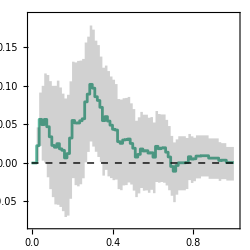

```mathematica
(* (b) F+(t) - F-(t) of the excursion durations for cfg["obsB"], bootstrap band; x = t/tmaxB (98% quantile of the durations) *)
excB = excursionsOut[traj, aState, nuOf[cfg["obsB"]]];
tauPlus = Pick[excB["duration"], excB["q"], 1];
tauMinus = Pick[excB["duration"], excB["q"], -1];
tmaxB = Quantile[Join[tauPlus, tauMinus], 0.98];
gridB = Subdivide[0., N@tmaxB, 80];
diffB = CDF[EmpiricalDistribution[tauPlus], gridB] - CDF[EmpiricalDistribution[tauMinus], gridB];
SeedRandom[3];
matB = Transpose@Table[
    CDF[EmpiricalDistribution[RandomChoice[tauPlus, Length[tauPlus]]], gridB] -
     CDF[EmpiricalDistribution[RandomChoice[tauMinus, Length[tauMinus]]], gridB], {1000}];
loB = Quantile[#, (1 - cl)/2] & /@ matB;
hiB = Quantile[#, 1 - (1 - cl)/2] & /@ matB;
Print["durations for ", cfg["obsB"], ": n(+1) = ", Length[tauPlus], ", n(-1) = ", Length[tauMinus], ",  KS p = ", KolmogorovSmirnovTest[tauPlus, tauMinus, "PValue"]];
diffplot = Show[
  ListLinePlot[staircase[gridB/tmaxB, diffB], PlotStyle -> green, ImageSize -> 250, AspectRatio -> 1,
   BaseStyle -> baseStyle,
   FrameLabel -> {tex["t/T_{\\max}"], tex["F_{+}(t)-F_{-}(t)"]},
   PlotRange -> {{0, 1.01}, {-0.08, 0.19}}],
  Graphics[{Opacity[0.18], Polygon[bandPolygon[gridB/tmaxB, loB, hiB]]}],
  Graphics[{Dashed, Line[{{0, 0}, {1, 0}}]}]]
```

```mathematica
(* (c) affinity: rigorous lower limit on ln P(+1)/P(-1) against the naive W (line) and its Poisson band from the 3 -> 4 count *)
lx0 = 0.; lx1 = 1.05;   (* x axis = t/T, fraction of the record *)
affTop = 10;
labelsA = tex[#, 17] & /@ {"\\ln P(+1)/P(-1)", "\\mathcal{A}_\\text{max}(+1)"};
legsA = Column[{PointLegend[{green}, {labelsA[[1]]}, LegendMarkerSize -> 17, Spacings -> .001, LegendMarkers -> "●"],
    LineLegend[{blue}, {labelsA[[2]]}, LegendMarkerSize -> 17, Spacings -> .001]}, Spacings -> -0.7];
affplot = Show[
  ListPlot[affSweep, PlotMarkers -> {Graphics[{green, Disk[]}], 0.05},
   BaseStyle -> baseStyle,
   FrameLabel -> {tex["t/T_{\\text{tot}}"], None},
   AspectRatio -> 1, ImageSize -> 250, PlotRange -> {{lx0, lx1}, {-0.1, 1.15 affTop}},
   Epilog -> Inset[legsA, Scaled[{.70, .88}]]],
  Graphics[{Opacity[0.15], blue, Rectangle[{lx0, affBand[[1]]}, {lx1, Min[affBand[[2]], affTop]}]}],
  If[naiveOK, Graphics[{blue, Thickness[0.006], Line[{{lx0, affNaive}, {lx1, affNaive}}]}], Graphics[{}]]]
```

-Graphics-

```mathematica
(* (d) entropy production: rigorous joint lower limit on sigma_exc against the naive W and its Poisson band *)
lx0 = 0.; lx1 = 1.05;
sigTop = 1.15 If[sigmaBand[[2]] === Infinity, 2 If[naiveOK, sigmaNaive, sigmaBand[[1]]], sigmaBand[[2]]];
labelsS = tex[#, 17] & /@ {"\\hat{\\sigma}_{\\text{exc}}", "\\sigma_{\\Delta t}"};
legsS = Column[{PointLegend[{green}, {labelsS[[1]]}, LegendMarkerSize -> 17, Spacings -> .001, LegendMarkers -> "●"],
    LineLegend[{yellow}, {labelsS[[2]]}, LegendMarkerSize -> 17, Spacings -> .001]}, Spacings -> -0.7];
sigplot = Show[
  ListPlot[sigSweep, PlotMarkers -> {Graphics[{green, Disk[]}], 0.05},
   BaseStyle -> baseStyle,
   FrameLabel -> {tex["t/T_{\\text{tot}}"], None},
   AspectRatio -> 1, ImageSize -> 250, PlotRange -> {{lx0, lx1}, {-0.01 sigTop, 1.13sigTop}},
   Epilog -> Inset[legsS, Scaled[{.70, .88}]]],
  Graphics[{Opacity[0.2], yellow, Rectangle[{lx0, sigmaBand[[1]]}, {lx1, Min[sigmaBand[[2]], sigTop]}]}],
  If[naiveOK, Graphics[{yellow, Thickness[0.006], Line[{{lx0, sigmaNaive}, {lx1, sigmaNaive}}]}], Graphics[{}]]]
```

-Graphics-

```mathematica
fig = If[DownValues[grid] =!= {},
   grid[{edgeplot, diffplot, affplot, sigplot}, 1, {0.14, 0.92}, 22],
   GraphicsRow[{edgeplot, diffplot, affplot, sigplot,occTrace, occHistLin}, ImageSize -> 1100]];
figs[cfg["id"]] = fig;
results[cfg["id"]] = <|"cfg" -> cfg, "traj" -> traj, "Ttot" -> Ttot, "W" -> Wnaive, "lnLo" -> lnLo, "sigLo" -> sigLo, "sweep" -> sweep|>;
fig
```

-Graphics-

```mathematica
Export[cfg["export"], fig]
```

results-6013.pdf

### Statistics quoted in the text

Numbers quoted in the text: p-values of panels (a), (b), detection time, directedness of the visits to state 4, the excursion statistics predicted by the naive W, and the significance of the gap between estimators and benchmark.

```mathematica
(* ---- (1) p-values of panels (a) and (b), observable cfg["obsB"] ----
   (a) frequencies: exact two-sided binomial test of P(+1) = P(-1) given n = n(+1) + n(-1).
   (b) durations:   two-sample Kolmogorov-Smirnov test of P(t|+1) = P(t|-1), plus a permutation p-value
                    (2 x 10^4 shuffles of the labels +1/-1 among the nonzero excursions), which makes no assumption on ties. *)
excS = excursionsOut[traj, aState, nuOf[cfg["obsB"]]];
tPs = Pick[excS["duration"], excS["q"], 1]; tMs = Pick[excS["duration"], excS["q"], -1];
(* exact two-sample KS distance, computed on the union of the observed values; fast enough for 2 x 10^4 shuffles *)
ksD[x_, y_] := Module[{e = Append[#, Last[#] + 1] &[Union[Join[x, y]]]},
   N@Max[Abs[Accumulate[BinCounts[x, {e}]]/Length[x] - Accumulate[BinCounts[y, {e}]]/Length[y]]]];
dObs = ksD[tPs, tMs];
SeedRandom[5];
permD = Module[{all = Join[tPs, tMs], np = Length[tPs], sh}, Table[sh = RandomSample[all]; ksD[sh[[;; np]], sh[[np + 1 ;;]]], {20000}]];
Print[Grid[{
    {"observable", "n(+1)", "n(-1)", "binomial p", "KS distance D", "KS p", "permutation p (20000 shuffles)"},
    {cfg["obsB"], Length[tPs], Length[tMs], binomP[Length[tPs], Length[tMs]], dObs,
     KolmogorovSmirnovTest[tPs, tMs, "PValue"], N[(1 + Count[permD, d_ /; d >= dObs])/(1 + Length[permD])]}}, Frame -> All]];
```

observable | n(+1) | n(-1) | binomial p | KS distance D | KS p | permutation p (20000 shuffles)
{1,3} | 284 | 323 | 0.122912 | 0.109558 | 0.0481108 | 0.0480476

```mathematica
(* ---- (2) how much data is needed to detect the violation, observable cfg["obsCD"] ----
   Excursions are ordered by their start time; for the first tm seconds of the record both tests are recomputed.
   tDetect = first time at which the binomial p-value drops below 10^-3 (and 10^-5). *)
excT = excursionsOut[traj, aState, nuOf[cfg["obsCD"]]];
qT = excT["q"]; durT = excT["duration"];
startT = traj[[excT["start"], 1]];                       (* start time of every excursion *)
detTable = Table[With[{m = Pick[Range[Length[qT]], Thread[startT <= tm]]},
    With[{qq = qT[[m]], dd = durT[[m]]},
     With[{a = Count[qq, 1], b = Count[qq, -1]},
      {tm, a, b, binomP[a, b],
       If[Min[a, b] >= 5, KolmogorovSmirnovTest[Pick[dd, qq, 1], Pick[dd, qq, -1], "PValue"], "-"]}]]],
   {tm, {5, 10, 20, 50, 100, 200, 500, 1000, Ttot}}];
Print[Grid[Prepend[detTable, {"first t (s)", "n(+1)", "n(-1)", "binomial p", "KS p"}], Frame -> All]];
(* exact detection time: scan the nonzero excursions in time order *)
nz = Pick[Range[Length[qT]], Unitize[qT], 1];
cumP = Accumulate[Boole[Positive /@ qT[[nz]]]];          (* running n(+1) *)
cumN = Range[Length[nz]] - cumP;                         (* running n(-1) *)
pRun = MapThread[binomP, {cumP, cumN}];
tDetect[lev_] := With[{k = FirstPosition[pRun, x_ /; x < lev, {Missing[]}][[1]]},
   If[MissingQ[k], {Missing["never"], Missing["never"]}, {startT[[nz[[k]]]], k}]];
Print["binomial p < 10^-3 first reached at t = ", tDetect[10^-3][[1]], " s, after ", tDetect[10^-3][[2]], " nonzero excursions"];
Print["binomial p < 10^-5 first reached at t = ", tDetect[10^-5][[1]], " s, after ", tDetect[10^-5][[2]], " nonzero excursions"];
```

first t (s) | n(+1) | n(-1) | binomial p | KS p
5 | 0 | 0 | 1. | -
10 | 0 | 0 | 1. | -
20 | 0 | 0 | 1. | -
50 | 0 | 0 | 1. | -
100 | 2 | 0 | 0.5 | -
200 | 2 | 0 | 0.5 | -
500 | 7 | 1 | 0.0703125 | -
1000 | 15 | 1 | 0.000518799 | -
1879.23 | 33 | 1 | 4.07454×10^-9 | -

binomial p < 10^-3 first reached at t = 958.587 s, after 15 nonzero excursions

binomial p < 10^-5 first reached at t = 1295. s, after 23 nonzero excursions

```mathematica
(* ---- (3) excursions through state 4 are directed ----
   Same test for observables on the edges of state 4. A time-symmetric artifact (noise, misassigned samples) produces
   equal counts in both directions, so a significant asymmetry means a directed, dissipative channel. *)
obs4 = {{2, 4}, {4, 3}, {1, 4}};
Print[Grid[Prepend[Table[With[{q = qOf[traj, e]}, With[{a = Count[q, _?Positive], b = Count[q, _?Negative]},
       {ToString[e[[1]]] <> " -> " <> ToString[e[[2]]], a, b, binomP[a, b]}]], {e, obs4}],
    {"observable (+1 for)", "n(+1)", "n(-1)", "binomial p"}], Frame -> All]];
Print["visits to state 4: ", Count[traj[[All, 2]], 4], ",  occupancy of state 4 (naive) = ", Tdw[[4]]/Total[Tdw]];
```

observable (+1 for) | n(+1) | n(-1) | binomial p
2 -> 4 | 30 | 1 | 2.98023×10^-8
4 -> 3 | 33 | 1 | 4.07454×10^-9
1 -> 4 | 7 | 5 | 0.774414

visits to state 4: 49,  occupancy of state 4 (naive) = 0.000725658

```mathematica
(* ---- (4) excursion statistics predicted by the naive rate matrix, against the measured ones ----
   The triangle-only row (states 1, 2, 3, same rates) is shown when the observable does not touch state 4. *)
pred = predictExcursions[Wnaive, aState, nuOf[cfg["obsCD"]]];
lnMeas = If[nPlus > 0 && nMinus > 0, Log[N[nPlus/nMinus]], "-"];
sigMeas = If[nPlus > 0 && nMinus > 0, ((nPlus - nMinus)/Ttot) Log[N[nPlus/nMinus]], "-"];
W3 = Wnaive[[1 ;; 3, 1 ;; 3]];
Print[Grid[DeleteCases[{
    {"", "A_max(+1)", "ln P(+1)/P(-1)", "sigma (1/s)", "sigma_exc (1/s)"},
    {"naive W, 4 states (prediction)", affNaive, pred["lnRatio"], sigmaNaive, pred["sigmaExc"]},
    If[FreeQ[cfg["obsCD"], 4],
     With[{p3 = predictExcursions[W3, aState, nuOf[cfg["obsCD"], 3]]},
      {"triangle 1-2-3 only (prediction)", affMax[W3, cfg["obsCD"]], p3["lnRatio"], EPR[W3], p3["sigmaExc"]}], Nothing],
    {"measured excursions", "", lnMeas, "", sigMeas}}, Nothing], Frame -> All]];
Print["check: excursion rate predicted from W = ", pred["K"], " /s,  measured = ", Length[qCD]/Ttot, " /s"];
```

| A_max(+1) | ln P(+1)/P(-1) | sigma (1/s) | sigma_exc (1/s)
naive W, 4 states (prediction) | 4.92694 | 4.617 | 0.0829221 | 0.0786108
measured excursions |  | 3.49651 |  | 0.0595395

check: excursion rate predicted from W = 0.79977 /s,  measured = 0.799265 /s

```mathematica
(* ---- (5) is the gap between the excursion estimators and the naive W significant? paired bootstrap ----
   Resample whole units (a visit to A plus the excursion that follows), recompute the naive W AND the excursion estimators
   from the same resample, and record the gaps; this keeps the correlation between the two sides. Needs enough reverse
   excursions, otherwise it is skipped. *)
If[nMinus >= 10, (
  iA = Flatten[Position[traj[[All, 2]], aState]];
  dV = Differences[Append[traj[[All, 1]], Ttot]];
  nuCD = nuOf[cfg["obsCD"]];
  unitStats = Table[Module[{a = iA[[k]], b = iA[[k + 1]], Nc = ConstantArray[0, {4, 4}], Td = ConstantArray[0., 4]},
     Do[Td[[traj[[j, 2]]]] += dV[[j]]; Nc[[traj[[j + 1, 2]], traj[[j, 2]]]] += 1, {j, a, b - 1}];
     {Nc, Td, Total[nuCD[[#[[2]], #[[1]]]] & /@ Partition[traj[[a ;; b, 2]], 2, 1]]}],
    {k, Length[iA] - 1}];
  gapStats[us_] := Module[{Nc = Total[us[[All, 1]]], Td = Total[us[[All, 2]]], q = us[[All, 3]], W, T, a, b, lr, sx},
    W = N[Nc/ConstantArray[Td, 4]]; T = Total[Td];
    a = Count[q, _?Positive]; b = Count[q, _?Negative]; lr = Log[a/b]; sx = ((a - b)/T) lr;
    {affMax[W, cfg["obsCD"]] - lr, EPR[W] - sx, lr/affMax[W, cfg["obsCD"]], sx/EPR[W]}];
  gap0 = gapStats[unitStats];
  SeedRandom[9];
  gapBoot = Table[gapStats[RandomChoice[unitStats, Length[unitStats]]], {300}];
  Print[Grid[{
     {"", "estimate", "95% interval", "fraction of resamples with gap <= 0"},
     {"A_naive - ln P(+1)/P(-1)", gap0[[1]], Quantile[gapBoot[[All, 1]], {0.025, 0.975}], N@Count[gapBoot[[All, 1]], x_ /; x <= 0]/300},
     {"sigma_naive - sigma_exc", gap0[[2]], Quantile[gapBoot[[All, 2]], {0.025, 0.975}], N@Count[gapBoot[[All, 2]], x_ /; x <= 0]/300},
     {"recovered fraction, affinity", gap0[[3]], Quantile[gapBoot[[All, 3]], {0.025, 0.975}], ""},
     {"recovered fraction, sigma", gap0[[4]], Quantile[gapBoot[[All, 4]], {0.025, 0.975}], ""}}, Frame -> All]]
  ), Print["(5) skipped: n(-1) = ", nMinus, " is too small for the paired bootstrap"]];
```

(5) skipped: n(-1) = 1 is too small for the paired bootstrap

## Positive bias: 0.705 V / 5515

Positive bias 0.705 V / 5515 (Supplemental Material). At this bias state 4 is visited often enough (about 0.8% of the samples) to form its own peak in the signal histogram, and a four-Gaussian fit resolves it: the occupation plot shows that (20) is a genuine charge state. Its dynamics are nearly reversible here (4 -> 3: 137/125), and the edges of state 4 carry only about 1% of the naive entropy production. Panels and statistics as for 5549.

### Configuration

```mathematica
cfg = <|
   "id" -> "5515",
   "dir" -> FileNameJoin[{dataRoot, "0.705_bias", "5515"}],
   "charge" -> {"(00)", "(10)", "(01)", "(20)"},          (* states 1, 2, 3, 4 at positive bias *)
   "rMax" -> 4, "minVisit" -> 2, "xFar" -> 4.5,          (* state assignment *)
   "obsA" -> {{1, 2}, {1, 3}, {2, 3}, {2, 4}, {4, 3}},   (* all edge observables (printed) *)
   "obsB" -> {1, 3},                                     (* panels (a), (b) *)
   "obsCD" -> {1, 3},                                    (* panels (c), (d): boundary observable of A = {3} *)
   "display" -> "bootstrap",                             (* estimates with bootstrap bars *)
   "fracs" -> Range[0.1, 1, 0.1],                        (* fractions t/T of the record for panels (c), (d) *)
   "bandEdge" -> None,
   "export" -> "results-5515.pdf"|>;
```

### Load and assign states

```mathematica
run = loadRun[cfg["dir"]];
tt = run["t"]; Ttot = Last[tt];
st = assignStatesPCA[run, cfg];
traj = st["traj"];
If[TrueQ[useSingleModel],
  With[{alt = assignFromFit[st["display"], tt, displayFitOf[st, cfg["id"]], cfg["minVisit"]]},
   traj = alt["traj"];
   Print["single model: states assigned from the display fit,  transit fraction = ", alt["transit"], ",  visits = ", Length[traj]]]];
```

samples = 111331,  duration = 1886.51 s,  mean dt = 0.0169452 s

PCA sign = 1,  levels of states 1, 2, 3 = {-0.686466,0.0725957,1.65365},  widths = {0.117243,0.182084,0.422926}  (standardised units)

candidates for state 4 = 8,  level of state 4 = 3.5613

transit fraction = 0.,  occupancy 1, 2, 3, 4 = {0.395892,0.314854,0.281422,0.0078325}

number of visits = 22173

General::munfl: 0.351765 4.389389880427×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.351765 3.872725739653×10^-317 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.351765 2.440966689596×10^-323 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

single model: states assigned from the display fit,  transit fraction = 0.,  visits = 22119

### Occupation plot

free fit of the four levels (display units): means = {-0.00647225,-0.000968777,0.0101603,0.0203363},  widths = {0.000803703,0.00160867,0.00201796,0.00128024},  weights = {0.39085,0.335855,0.265603,0.0076924}

General::munfl: 0.351765 4.389389880427×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.351765 3.872725739653×10^-317 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.351765 2.440966689596×10^-323 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

display fit (display units): means = {-0.00651078,-0.00106758,0.0108012,0.0206932},  widths = {0.000782113,0.000935905,0.00115316,0.00110668},  level weights = {0.370126,0.243864,0.205118,0.00569622},  mid-jump weights {{1,2},{1,3},{2,3},{1,4},{2,4},{3,4}} = {0.0473176,0.0549112,0.0567892,0.00964418,0.0062426,0.000291547},  total mid-jump = 0.175196

General::munfl: 0.354492 4.389389880427×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.354492 3.872725739653×10^-317 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.354492 2.440966689596×10^-323 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

log-likelihood of the display fit = 467008.;  without the Gaussian at level 4 it is lower by 615.303

General::munfl: 0.370126 4.90661×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.370126 5.866568186126×10^-309 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.370126 6.992239250008×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

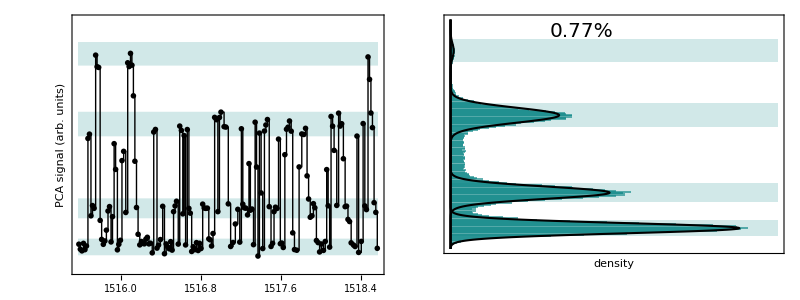
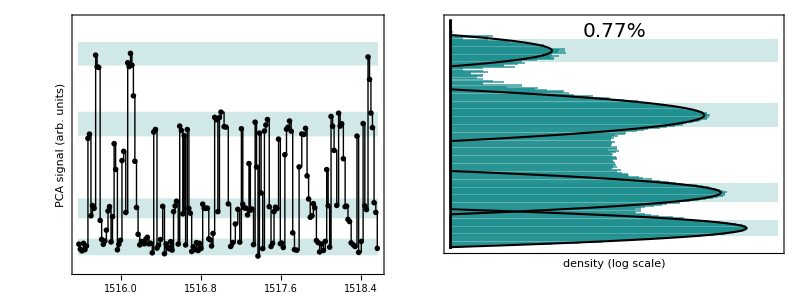

```mathematica
(* ---- occupation plot with a free fit of the four levels. At 0.705 V state 4 is common enough (about 0.8% of the samples)
   to form its own peak: a four-component Gaussian mixture, started from the assigned levels, is fitted to the whole record.
   A stretch of the PCA trace with the bands of the four levels (left), and the histogram of the whole record with the
   fitted levels (right), with a linear (occFigLin) and a logarithmic (occFigLog) density axis. The trace is shown with the
   sign used for the assignment (st["sign"]), so that the levels 1 < 2 < 3 < 4 run from bottom to top. ---- *)
tWin = {1515.57, 1518.57};                  (* s; three visits to 4 and dwells in 1, 2 and 3 *)
nSig = 1.5;                                 (* half-width of the shaded bands, in standard deviations of each level *)
yAll = st["display"];
{lev, wid, wts} = emFit1D[yAll, st["levels"], st["widths"], st["weights"]/Total[st["weights"]], 200];
Print["free fit of the four levels (display units): means = ", lev, ",  widths = ", wid, ",  weights = ", wts];
(* curves and bands: display fit with a Gaussian for each level and a mid-jump component between each pair of levels
   (emFitDetector in the Setup); the assignment levels lev, wid, wts set the plot range and the state-4 label *)
fitD = emFitDetector[yAll, lev, wid, wts, False, 300];
{levD, widD, wtsD} = Lookup[fitD, {"means", "widths", "weights"}];
Print["display fit (display units): means = ", levD, ",  widths = ", widD, ",  level weights = ", wtsD,
  ",  mid-jump weights ", fitD["pairs"], " = ", fitD["pairWeights"], ",  total mid-jump = ", Total[fitD["pairWeights"]]];
(* evidence for state 4: the same fit without the Gaussian at level 4 (jumps to and from level 4 still allowed) *)
fitNo4 = emFitDetector[yAll, lev, wid, wts, True, 300, {1, 2, 3}];
Print["log-likelihood of the display fit = ", fitD["logL"], ";  without the Gaussian at level 4 it is lower by ",
  fitD["logL"] - fitNo4["logL"]];
win = Select[Range[Length[tt]], tWin[[1]] <= tt[[#]] <= tWin[[2]] &];
yRange = {lev[[1]] - 4 wid[[1]], lev[[4]] + 4 wid[[4]]};
bandsT = Table[{Opacity[0.18], teal, Rectangle[{tWin[[1]], levD[[k]] - nSig widD[[k]]}, {tWin[[2]], levD[[k]] + nSig widD[[k]]}]}, {k, 4}];
occTrace = ListLinePlot[Transpose[{tt[[win]], yAll[[win]]}], InterpolationOrder -> 0,
   PlotStyle -> Directive[Black, AbsoluteThickness[1]], Mesh -> All, MeshStyle -> Directive[Black, AbsolutePointSize[4]],
   Prolog -> bandsT, Frame -> True, Axes -> False, PlotRange -> {tWin, yRange},
   FrameTicks -> {{None, Table[{levD[[k]], tex[cfg["charge"][[k]], 20]}, {k, 4}]}, {Automatic, None}},
   FrameLabel -> {{tnr["PCA signal (arb. units)"], None}, {tex["t\\ (\\mathrm{s})"], None}},
   BaseStyle -> baseStyle, AspectRatio -> Full, ImageSize -> {820, 300}, ImagePadding -> {{40, 70}, {65, 10}}];

binW = (yRange[[2]] - yRange[[1]])/200;
yIn = Select[yAll, yRange[[1]] <= # <= yRange[[2]] &];
{binsH, densH} = HistogramList[yIn, {yRange[[1]], yRange[[2]], binW}, "PDF"];
densH = densH Length[yIn]/Length[yAll];                (* density of the whole record *)
yGrid = Subdivide[yRange[[1]], yRange[[2]], 800];
gauss = Table[wtsD[[k]] PDF[NormalDistribution[levD[[k]], widD[[k]]], yGrid], {k, 4}];
mid = Sum[With[{a = fitD["pairs"][[j, 1]], b = fitD["pairs"][[j, 2]]},
    fitD["pairWeights"][[j]] boxPDF[yGrid, levD[[a]], levD[[b]], (widD[[a]] + widD[[b]])/2]], {j, Length[fitD["pairs"]]}];
total = Total[gauss] + mid;                            (* the full display fit *)
pctLabel[x_] := Text[Style[ToString[Round[100 wts[[4]], 0.01]] <> "%", 20, FontFamily -> "Times New Roman"], {x, lev[[4]] + 2.6 wid[[4]]}];

(* (i) linear density axis: the fourth peak is barely visible *)
xMaxH = 1.1 Max[densH];
bandsH = Table[{Opacity[0.18], teal, Rectangle[{0, levD[[k]] - nSig widD[[k]]}, {xMaxH, levD[[k]] + nSig widD[[k]]}]}, {k, 4}];
occHistLin = Show[
   Graphics[{bandsH, {Opacity[0.6], teal, EdgeForm[None],
      Table[Rectangle[{0, binsH[[i]]}, {densH[[i]], binsH[[i + 1]]}], {i, Length[densH]}]}}],
   (* linear panel: the Gaussian components of the display fit only (caption: "Gaussian components of a fit that
      also accounts for the samples recorded during jumps"); the log panel shows the full fit *)
   ListLinePlot[Table[Transpose[{gauss[[k]], yGrid}], {k, 4}], PlotStyle -> Directive[Black, AbsoluteThickness[1.5]]],
   Frame -> True, Axes -> False, FrameTicks -> None, PlotRange -> {{0, xMaxH}, yRange},
   FrameLabel -> {{None, None}, {tnr["density", 20], None}},
   Epilog -> pctLabel[0.4 xMaxH],
   AspectRatio -> Full, ImageSize -> {170, 300}, ImagePadding -> {{5, 10}, {65, 10}}];

(* (ii) logarithmic density axis: the fourth peak stands out *)
lMin = Log10[10^-3 Max[densH]]; lMax = Log10[2 Max[densH]];
lg[x_] := Max[Log10[Max[x, 10^-300]], lMin];           (* log10 of a density, clipped at the left edge of the panel *)
bandsH = Table[{Opacity[0.18], teal, Rectangle[{lMin, levD[[k]] - nSig widD[[k]]}, {lMax, levD[[k]] + nSig widD[[k]]}]}, {k, 4}];
occHistLog = Show[
   Graphics[{bandsH, {Opacity[0.6], teal, EdgeForm[None],
      Table[If[densH[[i]] > 0, Rectangle[{lMin, binsH[[i]]}, {lg[densH[[i]]], binsH[[i + 1]]}], {}], {i, Length[densH]}]}}],
   ListLinePlot[Table[Transpose[{lg /@ gauss[[k]], yGrid}], {k, 4}], PlotStyle -> Directive[Black, AbsoluteThickness[1.5]]],
   Frame -> True, Axes -> False, FrameTicks -> None, PlotRange -> {{lMin, lMax}, yRange},
   FrameLabel -> {{None, None}, {tnr["density (log scale)", 20], None}},
   Epilog -> pctLabel[lMin + 0.5 (lMax - lMin)],
   AspectRatio -> Full, ImageSize -> {170, 300}, ImagePadding -> {{5, 10}, {65, 10}}];

occFigLin = Grid[{{occTrace, occHistLin}}, Spacings -> 0];
occFigLog = Grid[{{occTrace, occHistLog}}, Spacings -> 0];
Column[{occFigLin, occFigLog}]
```

```mathematica
Export["occupation-5515-linear.pdf", occFigLin]
Export["occupation-5515-log.pdf", occFigLog]
```

occupation-5515-linear.pdf

occupation-5515-log.pdf

### Benchmarks

```mathematica
{Ncount, Tdw, Wnaive} = countJumps[traj, Ttot];
Print["jump counts N[[to, from]]:"]; Print[MatrixForm[Ncount]];
Print["dwell times (s) = ", Tdw, ",  occupations = ", Tdw/Total[Tdw]];
Print["naive W[[to, from]] (1/s):"]; Print[MatrixForm[Chop[Wnaive]]];
affNaive = affMax[Wnaive, cfg["obsCD"]];
sigmaNaive = EPR[Wnaive];
Print["naive benchmark: A_max(+1) for ", cfg["obsCD"], " = ", affNaive, ",  sigma = ", sigmaNaive, " /s"];
If[ListQ[cfg["bandEdge"]],
  affBand = rateBand[Wnaive, Ncount, Tdw, cfg["bandEdge"], affMax[#, cfg["obsCD"]] &];
  sigmaBand = rateBand[Wnaive, Ncount, Tdw, cfg["bandEdge"], EPR];
  Print["band from the count on edge ", cfg["bandEdge"], ":  A_max(+1) in ", affBand, ",  sigma in ", sigmaBand]];
(* if the rare reverse edge was never recorded, the naive W has a zero rate there: A_max(+1) is -Infinity and EPR drops the
   edge, so there is no naive point; panels (c), (d) then show only the band *)
naiveOK = ! (ListQ[cfg["bandEdge"]] && Ncount[[cfg["bandEdge"][[2]], cfg["bandEdge"][[1]]]] == 0);
(* contribution of each edge to the naive entropy production *)
piN = steadyState[Wnaive];
edgeSigma = Flatten[Table[With[{f = Wnaive[[b, a]] piN[[a]], r = Wnaive[[a, b]] piN[[b]]},
     {{a, b}, If[f > 0 && r > 0, (f - r) Log[f/r], Missing[]]}], {a, 4}, {b, a + 1, 4}], 1];
Print[Grid[Prepend[edgeSigma, {"edge", "contribution to sigma (1/s)"}], Frame -> All]];
Print["share of the naive sigma on the edges of the ring 1-2-3: ",
  Total[Cases[edgeSigma, {e_, v_?NumericQ} /; SubsetQ[{1, 2, 3}, e] :> v]]/sigmaNaive];
(* Table I of the Supplemental Material: the seven cycles of the four-state network, each in the orientation with
   positive affinity, and the outcome q of the observable cfg["obsCD"] along it *)
cycles7 = {{1, 3, 2, 1}, {1, 4, 2, 1}, {1, 4, 3, 1}, {2, 4, 3, 2}, {1, 2, 4, 3, 1}, {1, 3, 2, 4, 1}, {1, 4, 3, 2, 1}};
Print[Grid[Prepend[Table[With[{c = If[cycleAffinity[Wnaive, cc] >= 0, cc, Reverse[cc]]},
     {StringRiffle[ToString /@ c, " -> "], cycleAffinity[Wnaive, c],
      Total[nuOf[cfg["obsCD"]][[#[[2]], #[[1]]]] & /@ Partition[c, 2, 1]]}], {cc, cycles7}],
    {"cycle", "A_c", "q for " <> ToString[cfg["obsCD"]]}], Frame -> All]];
```

jump counts N[[to, from]]:

(0 | 5130 | 2690 | 211
4057 | 0 | 3142 | 236
3801 | 2010 | 0 | 197
173 | 296 | 175 | 0)

dwell times (s) = {825.517,589.152,444.963,26.8554},  occupations = {0.437595,0.312301,0.235869,0.0142357}

naive W[[to, from]] (1/s):

(0 | 8.70743 | 6.04545 | 7.8569
4.9145 | 0 | 7.06126 | 8.78781
4.60439 | 3.41168 | 0 | 7.33559
0.209566 | 0.502417 | 0.393291 | 0)

naive benchmark: A_max(+1) for {1,3} = 1.21754,  sigma = 0.617735 /s

edge | contribution to sigma (1/s)
{1,2} | 0.13338
{1,3} | 0.20345
{1,4} | 0.00399992
{2,3} | 0.268328
{2,4} | 0.0071994
{3,4} | 0.00137786

share of the naive sigma on the edges of the ring 1-2-3: 0.97964

cycle | A_c | q for {1, 3}
1 -> 3 -> 2 -> 1 | 1.02711 | 1
1 -> 2 -> 4 -> 1 | 0.190432 | 0
1 -> 3 -> 4 -> 1 | 0.425872 | 1
2 -> 4 -> 3 -> 2 | 0.79167 | 0
1 -> 3 -> 4 -> 2 -> 1 | 0.235439 | 1
1 -> 3 -> 2 -> 4 -> 1 | 1.21754 | 1
1 -> 4 -> 3 -> 2 -> 1 | 0.601238 | 0

### Excursions and estimators

```mathematica
qCD = qOf[traj, cfg["obsCD"]];
{nPlus, nMinus} = {Count[qCD, _?Positive], Count[qCD, _?Negative]};
Print["observable ", cfg["obsCD"], ":  excursions = ", Length[qCD], ",  n(+1), n(-1) = ", {nPlus, nMinus}, ",  binomial p = ", binomP[nPlus, nMinus]];
{lnLo, sigLo} = lowerLimits[qCD, Ttot];
Print["rigorous ", cl, " lower limits:  ln P(+1)/P(-1) >= ", lnLo, ",  sigma_exc >= ", sigLo, " /s"];
If[nPlus > 0 && nMinus > 0, SeedRandom[11]; Print["estimates with bootstrap ", cl, " intervals: ", estBoot[qCD, Ttot]]];
(* first f*T seconds of the record, for panels (c), (d); x = t/T *)
SeedRandom[11];
sweep = timeSweep[traj, cfg["obsCD"], cfg["display"], cfg["fracs"] Ttot];
affSweep = Cases[sweep, {t_, {v_, _}} :> {t/Ttot, v}];
sigSweep = Cases[sweep, {t_, {_, v_}} :> {t/Ttot, v}];
```

observable {1,3}:  excursions = 6007,  n(+1), n(-1) = {1755,644},  binomial p = 4.53089×10^-118

rigorous 0.95 lower limits:  ln P(+1)/P(-1) >= 0.925983,  sigma_exc >= 0.475051 /s

estimates with bootstrap 0.95 intervals: {1.000.090.09,0.590.100.10}

### Panels

observable | n(+1) | n(-1) | binomial p
1
2 | 653 | 1720 | 5.77155×10^-110
1
3 | 1755 | 644 | 4.53089×10^-118
2
3 | 619 | 1752 | 1.79041×10^-124
2
4 | 184 | 126 | 0.00117148
4
3 | 140 | 118 | 0.190975

n(+1), n(-1) = {1755,644},  binomial p = 4.53089×10^-118,  KS distance = 0.0627135,  KS p (durations) = 0.0491594

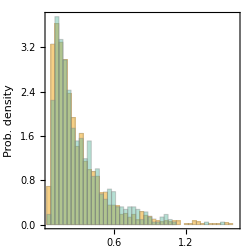

```mathematica
(* (a) duration distributions P(t|+1), P(t|-1) for cfg["obsB"] (here 1 -> 3); inset: number of excursions with q = +1
   (net 1 -> 3) and q = -1 (net 3 -> 1), Garwood bars. Both P(q) != P(-q) and P(t|q) != P(t|-q) violate detailed balance.
   The counts for every edge observable are printed first. *)
obsList = cfg["obsA"];
obsCounts = Table[With[{q = qOf[traj, e]}, {Count[q, _?Positive], Count[q, _?Negative]}], {e, obsList}];
Print[TableForm[Table[{obsList[[i]], obsCounts[[i, 1]], obsCounts[[i, 2]], binomP @@ obsCounts[[i]]}, {i, Length[obsList]}],
   TableHeadings -> {None, {"observable", "n(+1)", "n(-1)", "binomial p"}}]];

excA = excursionsOut[traj, aState, nuOf[cfg["obsB"]]];
tP = Pick[excA["duration"], excA["q"], 1]; tM = Pick[excA["duration"], excA["q"], -1];
{nP, nM} = {Length[tP], Length[tM]};
Print["n(+1), n(-1) = ", {nP, nM}, ",  binomial p = ", binomP[nP, nM],
  ",  KS distance = ", KolmogorovSmirnovTest[tP, tM, "TestStatistic"], ",  KS p (durations) = ", KolmogorovSmirnovTest[tP, tM, "PValue"]];

tCut = Quantile[Join[tP, tM], 0.99];                  (* x range of the histogram *)
binWt = 2 Mean[Differences[tt]];                      (* bin width = 2 samples: avoids aliasing with the sampling grid *)
legsH = SwatchLegend[{yellow, green}, tex[#, 17] & /@ {"P(t\\,|+1)", "P(t\\,|-1)"}, LegendMarkerSize -> 14, Spacings -> .001];
ciP = poissonCI[nP, cl]; ciM = poissonCI[nM, cl];
insetBars = Graphics[{
    {yellow, EdgeForm[None], Rectangle[{0.6, 0}, {1.4, nP}]},
    {green, EdgeForm[None], Rectangle[{1.6, 0}, {2.4, nM}]},
    {GrayLevel[0.25], Thickness[0.012], Line[{{1, ciP[[1]]}, {1, ciP[[2]]}}], Line[{{2, ciM[[1]]}, {2, ciM[[2]]}}]},
    Text[Style[nP, 11, FontFamily -> "Times New Roman"], {1, ciP[[2]] + 0.09 nP}],
    Text[Style[nM, 11, FontFamily -> "Times New Roman"], {2, ciM[[2]] + 0.09 nP}]},
   Frame -> True, AspectRatio -> 1, PlotRange -> {{0.3, 2.7}, {0, 1.25 nP}},
   FrameTicks -> {{None, None}, {{{1, tex["1\\to 3", 13]}, {2, tex["3\\to 1", 13]}}, None}},
   BaseStyle -> {FontSize -> 12, FontFamily -> "Times New Roman"}, ImageSize -> 150];
edgeplot = Histogram[{tP, tM}, {0, Max[Join[tP, tM]] + binWt, binWt}, "PDF",
   ChartLayout -> "Overlapped",
   ChartStyle -> {Directive[Opacity[0.6], yellow, EdgeForm[GrayLevel[0.5]]], Directive[Opacity[0.45], green, EdgeForm[GrayLevel[0.5]]]},
   Frame -> True, AspectRatio -> 1, ImageSize -> 250,
   PlotRange -> {{0.05, 1.45 tCut}, All},
   BaseStyle -> baseStyle,
   FrameLabel -> {tex["t\\ (\\mathrm{s})"], tnr["Prob. density"]},
   Epilog -> {Inset[insetBars, Scaled[{0.77, 0.72}], Center, Scaled[{0.48, 0.48}]], Inset[legsH, Scaled[{0.77, 0.25}]]}]
```

durations for {1,3}: n(+1) = 1755, n(-1) = 644,  KS p = 0.0491594

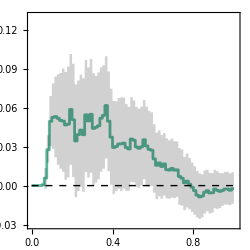

```mathematica
(* (b) F+(t) - F-(t) of the excursion durations for cfg["obsB"], bootstrap band; x = t/tmaxB (98% quantile of the durations) *)
excB = excursionsOut[traj, aState, nuOf[cfg["obsB"]]];
tauPlus = Pick[excB["duration"], excB["q"], 1];
tauMinus = Pick[excB["duration"], excB["q"], -1];
tmaxB = Quantile[Join[tauPlus, tauMinus], 0.98];
gridB = Subdivide[0., N@tmaxB, 80];
diffB = CDF[EmpiricalDistribution[tauPlus], gridB] - CDF[EmpiricalDistribution[tauMinus], gridB];
SeedRandom[3];
matB = Transpose@Table[
    CDF[EmpiricalDistribution[RandomChoice[tauPlus, Length[tauPlus]]], gridB] -
     CDF[EmpiricalDistribution[RandomChoice[tauMinus, Length[tauMinus]]], gridB], {1000}];
loB = Quantile[#, (1 - cl)/2] & /@ matB;
hiB = Quantile[#, 1 - (1 - cl)/2] & /@ matB;
Print["durations for ", cfg["obsB"], ": n(+1) = ", Length[tauPlus], ", n(-1) = ", Length[tauMinus], ",  KS p = ", KolmogorovSmirnovTest[tauPlus, tauMinus, "PValue"]];
diffplot = Show[
  ListLinePlot[staircase[gridB/tmaxB, diffB], PlotStyle -> green, ImageSize -> 250, AspectRatio -> 1,
   BaseStyle -> baseStyle,
   FrameLabel -> {tex["t/T_{\\max}"], tex["F_{+}(t)-F_{-}(t)"]},
   PlotRange -> {{0, 1.01}, {-0.03, 0.13}}],
  Graphics[{Opacity[0.18], Polygon[bandPolygon[gridB/tmaxB, loB, hiB]]}],
  Graphics[{Dashed, Line[{{0, 0}, {1, 0}}]}]]
```

```mathematica
(* (c) affinity: estimate with bootstrap bars against the naive W (dashed) *)
lx0 = 0.; lx1 = 1.05;   (* x axis = t/T, fraction of the record *)
affBot = 0.6; affTop = 1.6;
labelsA = tex[#, 17] & /@ {"\\ln P(1)/P(-1)", "\\mathcal{A}_{\\text{max}}(+1)"};
legsA = Column[{PointLegend[{green}, {labelsA[[1]]}, LegendMarkerSize -> 17, Spacings -> .001, LegendMarkers -> "●"],
    LineLegend[{Directive[blue, Dashed]}, {labelsA[[2]]}, LegendMarkerSize -> 17, Spacings -> .001]}, Spacings -> -0.7];
affplot = Show[
  ListPlot[affSweep, PlotMarkers -> {Graphics[{green, Disk[]}], 0.05}, IntervalMarkersStyle -> {Directive[green]},
   BaseStyle -> baseStyle,
   FrameLabel -> {tex["t/T_{\\rm tot}"], None},
   AspectRatio -> 1, ImageSize -> 250, PlotRange -> {{lx0, lx1}, {affBot, affTop}},
   Epilog -> Inset[legsA, Scaled[{.72, .86}]]],
  Graphics[{blue, Dashed, Thickness[0.01], Line[{{lx0, affNaive}, {lx1, affNaive}}]}]]
```

-Graphics-

```mathematica
(* (d) entropy production: estimate with bootstrap bars against the naive W (dashed) *)
lx0 = 0.; lx1 = 1.05;
sigBot = 0.2; sigTop = 1.2;
labelsS = tex[#, 17] & /@ {"\\hat{\\sigma}_{\\text{exc}}", "\\sigma_{\\Delta_t}"};
legsS = Column[{PointLegend[{green}, {labelsS[[1]]}, LegendMarkerSize -> 17, Spacings -> .001, LegendMarkers -> "●"],
    LineLegend[{Directive[yellow, Dashed]}, {labelsS[[2]]}, LegendMarkerSize -> 17, Spacings -> .001]}, Spacings -> -0.7];
sigplot = Show[
  ListPlot[sigSweep, PlotMarkers -> {Graphics[{green, Disk[]}], 0.05}, IntervalMarkersStyle -> {Directive[green]},
   BaseStyle -> baseStyle,
   FrameLabel -> {tex["t/T_{\\rm tot}"], None},
   AspectRatio -> 1, ImageSize -> 250, PlotRange -> {{lx0, lx1}, {sigBot, sigTop}},
   Epilog -> Inset[legsS, Scaled[{.72, .86}]]],
  Graphics[{yellow, Dashed, Thickness[0.01], Line[{{lx0, sigmaNaive}, {lx1, sigmaNaive}}]}]]
```

-Graphics-

### Statistics quoted in the text

Numbers quoted in the text: p-values of panels (a), (b), detection time, directedness of the visits to state 4, the excursion statistics predicted by the naive W, and the significance of the gap between estimators and benchmark.

```mathematica
(* ---- (1) p-values of panels (a) and (b), observable cfg["obsB"] ----
   (a) frequencies: exact two-sided binomial test of P(+1) = P(-1) given n = n(+1) + n(-1).
   (b) durations:   two-sample Kolmogorov-Smirnov test of P(t|+1) = P(t|-1), plus a permutation p-value
                    (2 x 10^4 shuffles of the labels +1/-1 among the nonzero excursions), which makes no assumption on ties. *)
excS = excursionsOut[traj, aState, nuOf[cfg["obsB"]]];
tPs = Pick[excS["duration"], excS["q"], 1]; tMs = Pick[excS["duration"], excS["q"], -1];
(* exact two-sample KS distance, computed on the union of the observed values; fast enough for 2 x 10^4 shuffles *)
ksD[x_, y_] := Module[{e = Append[#, Last[#] + 1] &[Union[Join[x, y]]]},
   N@Max[Abs[Accumulate[BinCounts[x, {e}]]/Length[x] - Accumulate[BinCounts[y, {e}]]/Length[y]]]];
dObs = ksD[tPs, tMs];
SeedRandom[5];
permD = Module[{all = Join[tPs, tMs], np = Length[tPs], sh}, Table[sh = RandomSample[all]; ksD[sh[[;; np]], sh[[np + 1 ;;]]], {20000}]];
Print[Grid[{
    {"observable", "n(+1)", "n(-1)", "binomial p", "KS distance D", "KS p", "permutation p (20000 shuffles)"},
    {cfg["obsB"], Length[tPs], Length[tMs], binomP[Length[tPs], Length[tMs]], dObs,
     KolmogorovSmirnovTest[tPs, tMs, "PValue"], N[(1 + Count[permD, d_ /; d >= dObs])/(1 + Length[permD])]}}, Frame -> All]];
```

observable | n(+1) | n(-1) | binomial p | KS distance D | KS p | permutation p (20000 shuffles)
{1,3} | 1755 | 644 | 4.53089×10^-118 | 0.0627135 | 0.0491594 | 0.0453477

```mathematica
(* ---- (2) how much data is needed to detect the violation, observable cfg["obsCD"] ----
   Excursions are ordered by their start time; for the first tm seconds of the record both tests are recomputed.
   tDetect = first time at which the binomial p-value drops below 10^-3 (and 10^-5). *)
excT = excursionsOut[traj, aState, nuOf[cfg["obsCD"]]];
qT = excT["q"]; durT = excT["duration"];
startT = traj[[excT["start"], 1]];                       (* start time of every excursion *)
detTable = Table[With[{m = Pick[Range[Length[qT]], Thread[startT <= tm]]},
    With[{qq = qT[[m]], dd = durT[[m]]},
     With[{a = Count[qq, 1], b = Count[qq, -1]},
      {tm, a, b, binomP[a, b],
       If[Min[a, b] >= 5, KolmogorovSmirnovTest[Pick[dd, qq, 1], Pick[dd, qq, -1], "PValue"], "-"]}]]],
   {tm, {5, 10, 20, 50, 100, 200, 500, 1000, Ttot}}];
Print[Grid[Prepend[detTable, {"first t (s)", "n(+1)", "n(-1)", "binomial p", "KS p"}], Frame -> All]];
(* exact detection time: scan the nonzero excursions in time order *)
nz = Pick[Range[Length[qT]], Unitize[qT], 1];
cumP = Accumulate[Boole[Positive /@ qT[[nz]]]];          (* running n(+1) *)
cumN = Range[Length[nz]] - cumP;                         (* running n(-1) *)
pRun = MapThread[binomP, {cumP, cumN}];
tDetect[lev_] := With[{k = FirstPosition[pRun, x_ /; x < lev, {Missing[]}][[1]]},
   If[MissingQ[k], {Missing["never"], Missing["never"]}, {startT[[nz[[k]]]], k}]];
Print["binomial p < 10^-3 first reached at t = ", tDetect[10^-3][[1]], " s, after ", tDetect[10^-3][[2]], " nonzero excursions"];
Print["binomial p < 10^-5 first reached at t = ", tDetect[10^-5][[1]], " s, after ", tDetect[10^-5][[2]], " nonzero excursions"];
```

first t (s) | n(+1) | n(-1) | binomial p | KS p
5 | 7 | 2 | 0.179688 | -
10 | 11 | 7 | 0.480682 | 0.730266
20 | 16 | 8 | 0.15159 | 0.887679
50 | 46 | 17 | 0.000336709 | 0.860715
100 | 86 | 33 | 1.26676×10^-6 | 0.313561
200 | 179 | 67 | 5.82807×10^-13 | 0.4446
500 | 454 | 154 | 2.85374×10^-35 | 0.734831
1000 | 886 | 317 | 1.16837×10^-62 | 0.260981
1886.51 | 1755 | 644 | 4.53089×10^-118 | 0.0491594

binomial p < 10^-3 first reached at t = 42.675 s, after 50 nonzero excursions

binomial p < 10^-5 first reached at t = 78.855 s, after 96 nonzero excursions

```mathematica
(* ---- (3) excursions through state 4 are directed ----
   Same test for observables on the edges of state 4. A time-symmetric artifact (noise, misassigned samples) produces
   equal counts in both directions, so a significant asymmetry means a directed, dissipative channel. *)
obs4 = {{2, 4}, {4, 3}, {1, 4}};
Print[Grid[Prepend[Table[With[{q = qOf[traj, e]}, With[{a = Count[q, _?Positive], b = Count[q, _?Negative]},
       {ToString[e[[1]]] <> " -> " <> ToString[e[[2]]], a, b, binomP[a, b]}]], {e, obs4}],
    {"observable (+1 for)", "n(+1)", "n(-1)", "binomial p"}], Frame -> All]];
Print["visits to state 4: ", Count[traj[[All, 2]], 4], ",  occupancy of state 4 (naive) = ", Tdw[[4]]/Total[Tdw]];
```

observable (+1 for) | n(+1) | n(-1) | binomial p
2 -> 4 | 184 | 126 | 0.00117148
4 -> 3 | 140 | 118 | 0.190975
1 -> 4 | 112 | 150 | 0.0220817

visits to state 4: 644,  occupancy of state 4 (naive) = 0.0142357

```mathematica
(* ---- (4) excursion statistics predicted by the naive rate matrix, against the measured ones ----
   The triangle-only row (states 1, 2, 3, same rates) is shown when the observable does not touch state 4. *)
pred = predictExcursions[Wnaive, aState, nuOf[cfg["obsCD"]]];
lnMeas = If[nPlus > 0 && nMinus > 0, Log[N[nPlus/nMinus]], "-"];
sigMeas = If[nPlus > 0 && nMinus > 0, ((nPlus - nMinus)/Ttot) Log[N[nPlus/nMinus]], "-"];
W3 = Wnaive[[1 ;; 3, 1 ;; 3]];
Print[Grid[DeleteCases[{
    {"", "A_max(+1)", "ln P(+1)/P(-1)", "sigma (1/s)", "sigma_exc (1/s)"},
    {"naive W, 4 states (prediction)", affNaive, pred["lnRatio"], sigmaNaive, pred["sigmaExc"]},
    If[FreeQ[cfg["obsCD"], 4],
     With[{p3 = predictExcursions[W3, aState, nuOf[cfg["obsCD"], 3]]},
      {"triangle 1-2-3 only (prediction)", affMax[W3, cfg["obsCD"]], p3["lnRatio"], EPR[W3], p3["sigmaExc"]}], Nothing],
    {"measured excursions", "", lnMeas, "", sigMeas}}, Nothing], Frame -> All]];
Print["check: excursion rate predicted from W = ", pred["K"], " /s,  measured = ", Length[qCD]/Ttot, " /s"];
```

| A_max(+1) | ln P(+1)/P(-1) | sigma (1/s) | sigma_exc (1/s)
naive W, 4 states (prediction) | 1.21754 | 0.987407 | 0.617735 | 0.581303
triangle 1-2-3 only (prediction) | 1.02711 | 1.02711 | 0.613545 | 0.613545
measured excursions |  | 1.00253 |  | 0.590406

check: excursion rate predicted from W = 3.18464 /s,  measured = 3.18419 /s

```mathematica
(* ---- (5) is the gap between the excursion estimators and the naive W significant? paired bootstrap ----
   Resample whole units (a visit to A plus the excursion that follows), recompute the naive W AND the excursion estimators
   from the same resample, and record the gaps; this keeps the correlation between the two sides. Needs enough reverse
   excursions, otherwise it is skipped. *)
If[nMinus >= 10, (
  iA = Flatten[Position[traj[[All, 2]], aState]];
  dV = Differences[Append[traj[[All, 1]], Ttot]];
  nuCD = nuOf[cfg["obsCD"]];
  unitStats = Table[Module[{a = iA[[k]], b = iA[[k + 1]], Nc = ConstantArray[0, {4, 4}], Td = ConstantArray[0., 4]},
     Do[Td[[traj[[j, 2]]]] += dV[[j]]; Nc[[traj[[j + 1, 2]], traj[[j, 2]]]] += 1, {j, a, b - 1}];
     {Nc, Td, Total[nuCD[[#[[2]], #[[1]]]] & /@ Partition[traj[[a ;; b, 2]], 2, 1]]}],
    {k, Length[iA] - 1}];
  gapStats[us_] := Module[{Nc = Total[us[[All, 1]]], Td = Total[us[[All, 2]]], q = us[[All, 3]], W, T, a, b, lr, sx},
    W = N[Nc/ConstantArray[Td, 4]]; T = Total[Td];
    a = Count[q, _?Positive]; b = Count[q, _?Negative]; lr = Log[a/b]; sx = ((a - b)/T) lr;
    {affMax[W, cfg["obsCD"]] - lr, EPR[W] - sx, lr/affMax[W, cfg["obsCD"]], sx/EPR[W]}];
  gap0 = gapStats[unitStats];
  SeedRandom[9];
  gapBoot = Table[gapStats[RandomChoice[unitStats, Length[unitStats]]], {300}];
  Print[Grid[{
     {"", "estimate", "95% interval", "fraction of resamples with gap <= 0"},
     {"A_naive - ln P(+1)/P(-1)", gap0[[1]], Quantile[gapBoot[[All, 1]], {0.025, 0.975}], N@Count[gapBoot[[All, 1]], x_ /; x <= 0]/300},
     {"sigma_naive - sigma_exc", gap0[[2]], Quantile[gapBoot[[All, 2]], {0.025, 0.975}], N@Count[gapBoot[[All, 2]], x_ /; x <= 0]/300},
     {"recovered fraction, affinity", gap0[[3]], Quantile[gapBoot[[All, 3]], {0.025, 0.975}], ""},
     {"recovered fraction, sigma", gap0[[4]], Quantile[gapBoot[[All, 4]], {0.025, 0.975}], ""}}, Frame -> All]]
  ), Print["(5) skipped: n(-1) = ", nMinus, " is too small for the paired bootstrap"]];
```

| estimate | 95% interval | fraction of resamples with gap <= 0
A_naive - ln P(+1)/P(-1) | 0.215514 | {0.0146614,0.460876} | 0.00666667
sigma_naive - sigma_exc | 0.0278473 | {0.000519227,0.0602866} | 0.0233333
recovered fraction, affinity | 0.823065 | {0.684408,0.985837} | 
recovered fraction, sigma | 0.954961 | {0.904829,0.999237} |

## Benchmark on emulated experiments

Benchmark of the estimators on emulated experiments (Supplemental Material). The data have no ground truth, so we emulate them: ten random models built from random fundamental affinities, with rates and occupations in the range of the three runs, each simulated for 1915 s and recorded by a detector with the sampling interval, levels and noise of 5549. Each record goes through the same pipeline as the data, and four estimates of A_max and sigma are compared: the ground truth, a Baum-Welch fit of a hidden Markov model to the raw signal, the naive W, and the excursion estimators for 1 <-> 3. All random numbers follow from benchSeed, set at the top of the Estimates cell: change it and evaluate Estimates and Plots again for a new set of models. Evaluate the Setup section first.

### Models and emulator

```mathematica
(* ---- emulated experiments: models, trajectories and detector ---- *)
(* Random 4-state models, all-to-all, built from their fundamental affinities. Spanning tree {1-2, 2-3, 2-4}; the chords
   1 -> 3, 3 -> 4 and 1 -> 4 close the fundamental cycles 1 -> 3 -> 2 -> 1, 3 -> 4 -> 2 -> 3 and 1 -> 4 -> 2 -> 1, of
   affinities F[[1]], F[[2]], F[[3]]. Rates: W(x -> y) = k_xy Exp[(E_x - E_y)/2 + f_xy/2], with symmetric kinetic parameters
   k_xy, state energies E_x, and f_xy = F_c on the chord of the cycle c (f_yx = -f_xy, 0 on the tree). The energies cancel
   around every cycle, so each fundamental cycle has affinity F_c exactly; they keep state 4 rare, as in the data. *)
benchEdges = {{1, 2}, {2, 3}, {2, 4}, {1, 3}, {3, 4}, {1, 4}};
benchChords = {{1, 3}, {3, 4}, {1, 4}};
buildModel[k_, en_, F_] := Module[{W = ConstantArray[0., {4, 4}], x, y, f},
   Do[{x, y} = benchEdges[[e]];
    f = If[MemberQ[benchChords, {x, y}], F[[First@FirstPosition[benchChords, {x, y}]]], 0.];
    W[[y, x]] = k[[e]] Exp[(en[[x]] - en[[y]])/2 + f/2];
    W[[x, y]] = k[[e]] Exp[(en[[y]] - en[[x]])/2 - f/2], {e, Length[benchEdges]}];
   W];

(* experimental window, from the three runs: every rate <= 40 /s, escape rates of states 1, 2, 3 between 3 and 20 /s,
   occupations of states 1, 2, 3 between 0.1 and 0.55 (0.11 to 0.56 in the data) and of state 4 between 0.1% and 2% *)
modelOK[W_] := With[{p = steadyState[W], esc = Total[offDiag[W]]},
   Max[W] <= 40 && AllTrue[esc[[;; 3]], 3 <= # <= 20 &] && AllTrue[p[[;; 3]], 0.1 <= # <= 0.55 &] && 0.001 <= p[[4]] <= 0.02];

(* draw until the model is in the window: k log-uniform in [0.5, 10] /s, E_1, E_2, E_3 uniform in [-1, 1], E_4 in [4, 7],
   F uniform in [-5, 5]. Returns {W, F}. *)
drawModelF[] := Module[{k, en, F, W, ok = False},
   While[! ok,
    k = Exp[RandomReal[{Log[0.5], Log[10.]}, 6]];
    en = Join[RandomReal[{-1, 1}, 3], {RandomReal[{4, 7}]}];
    F = RandomReal[{-5, 5}, 3];
    W = buildModel[k, en, F]; ok = modelOK[W]];
   {W, F}];

(* detector of the emulated experiment: the sampling interval, duration, levels and noise of 5549 (standardised units).
   Each sample is the level averaged over its sampling interval plus white Gaussian noise, so a jump inside an interval
   gives a sample between two levels, as in the data. *)
benchDt = 0.0172; benchT = 1915.;
benchLevels = {-0.72, 0.01, 1.33, 2.33}; benchNoise = 0.11;
benchCfg = <|"rMax" -> 4, "minVisit" -> 2, "xFar" -> 4.5|>;   (* state assignment, as for the data *)

(* continuous-time trajectory of W[[to, from]] over [0, T]: jump times ts (ts[[1]] = 0) and states xs *)
gillespieRun[W_, T_, x0_] := Module[{w = offDiag[N[W]], gam, t = 0., x = x0, out},
   gam = Total[w];
   out = Reap[Sow[{0., x0}];
      While[(t += RandomVariate[ExponentialDistribution[gam[[x]]]]) < T,
       x = RandomChoice[w[[All, x]] -> Range[Length[w]]]; Sow[{t, x}]]][[2, 1]];
   {out[[All, 1]], out[[All, 2]]}];

(* detector: sample j averages the level over [(j - 1) dt, j dt]; F is the integral of the level, piecewise linear *)
detectorSignal[ts_, xs_, T_, dt_, levels_, noise_] := Module[{tb = Append[ts, T], F, edges, Fe},
   F = Prepend[Accumulate[levels[[xs]] Differences[tb]], 0.];
   edges = Range[0., T, dt];
   Fe = Interpolation[Transpose[{tb, F}], InterpolationOrder -> 1][edges];
   {Most[edges], Differences[Fe]/dt + noise RandomVariate[NormalDistribution[], Length[edges] - 1]}];

(* entropy production restricted to the states that are entered and left (a state missed by the assignment has a zero
   row and column in the naive W, which makes steadyState singular); identical to EPR when every state is resolved *)
eprActive[W_] := With[{w = offDiag[N[W]]},
   With[{act = Select[Range[Length[w]], Total[w[[All, #]]] > 0 && Total[w[[#]]] > 0 &]}, If[Length[act] < 2, 0., EPR[w[[act, act]]]]]];
```

### Baum-Welch fit

```mathematica
(* ---- Baum-Welch fit of a 4-state hidden Markov model with Gaussian emissions to the raw signal ---- *)
(* Discrete-time chain P[[from, to]] at the sampling interval; scaled forward and backward recursions (compiled):
   a[[t]] = normalised forward vector, c[[t]] its normaliser, b[[t]] = backward vector divided by the later normalisers,
   so that a b is the posterior of the hidden state and Total[Log[c]] the log-likelihood. *)
hmmForward = Compile[{{P, _Real, 2}, {p0, _Real, 1}, {B, _Real, 2}},
   Module[{n = Length[B], a, v},
    a = Table[0., {n}, {Length[p0]}];
    v = p0 B[[1]]; a[[1]] = v/Total[v];
    Do[v = (a[[t - 1]] . P) B[[t]]; a[[t]] = v/Total[v], {t, 2, n}];
    a]];
hmmBackward = Compile[{{P, _Real, 2}, {B, _Real, 2}, {c, _Real, 1}},
   Module[{n = Length[B], b},
    b = Table[1., {n}, {Length[P]}];
    Do[b[[t]] = (P . (B[[t + 1]] b[[t + 1]]))/c[[t + 1]], {t, n - 1, 1, -1}];
    b]];

(* EM iterations until the log-likelihood gains less than tol. Start: means mu0 and widths sd0 (from the state
   assignment), P with 0.97 on the diagonal. The hidden states are sorted by their means, so state k is the k-th level.
   The generator follows from W = MatrixLog[P]/dt; negative off-diagonal rates (P not embeddable) are set to 0.
   Returns <|"W" -> W[[to, from]], "means", "widths", "iterations", "negative rates"|>. *)
baumWelchW[y_, mu0_, sd0_, dt_, maxIter_ : 300, tol_ : 10^-3] := Module[
   {k = Length[mu0], mu = N[mu0], sd = N[sd0], p0, P, B, a, b, c, g, xi, Nk, ll = -Infinity, llNew, it = 0, o, L, nneg},
   p0 = ConstantArray[1./k, k];
   P = (0.97 - 0.01) IdentityMatrix[k] + 0.01; P = P/Total[P, {2}];
   While[it < maxIter,
    it++;
    B = Transpose[Table[Exp[-((y - mu[[j]])/sd[[j]])^2/2]/(sd[[j]] Sqrt[2. Pi]), {j, k}]];
    B = Clip[B, {1.*^-300, 1.*^300}];
    a = hmmForward[P, p0, B];
    c = Prepend[Total[(Most[a] . P) Rest[B], {2}], Total[p0 B[[1]]]];
    b = hmmBackward[P, B, c];
    g = a b; g = g/Total[g, {2}];
    xi = P (Transpose[Most[a]] . (Rest[B] Rest[b]/Rest[c]));
    P = xi/Total[xi, {2}]; p0 = g[[1]];
    Nk = Total[g];
    mu = (y . g)/Nk;
    sd = Table[Sqrt[(g[[All, j]] . (y - mu[[j]])^2)/Nk[[j]]], {j, k}];
    llNew = Total[Log[c]];
    If[llNew - ll < tol, Break[]]; ll = llNew];
   o = Ordering[mu]; P = P[[o, o]];
   L = offDiag[Chop[Re[MatrixLog[Transpose[P]]]]/dt];          (* [[to, from]] *)
   nneg = Count[Flatten[L], x_ /; x < 0];
   <|"W" -> Map[Max[#, 0.] &, L, {2}], "means" -> mu[[o]], "widths" -> sd[[o]], "iterations" -> it, "negative rates" -> nneg|>];
```

### Estimates

```mathematica
(* ---- the four estimates for each model ----
   ground truth : A_max of the cycles through the observable and sigma, from the model W
   Baum-Welch   : the same from the generator of the hidden Markov fit to the raw signal
   naive        : the same from countJumps on the assigned trajectory (the benchmark used for the data)
   excursions   : ln P(+1)/P(-1) and sigma_exc on the assigned trajectory, A = {3}, with bootstrap intervals
   Region A = {aState} = {3}, region B = {1, 2, 4}. The observable 1 <-> 3 is oriented along the true net current: 1 -> 3, or 3 -> 1 when the model drives 3 -> 1.
   "ideal" is the excursion value at perfect time resolution (predictExcursions), printed for reference.
   A few seconds per model, most of it in the Baum-Welch fit. *)
nModels = 10;
benchSeed = 4;   (* the only seed: models, trajectories, detector noise and bootstrap all follow from it; change it for a new run, plot seed 777 *)
SeedRandom[benchSeed]; Print["seed = ", benchSeed];
bench = Table[
   Module[{W, F, obs, ts, xs, t, sig, st, y, mu0, sd0, Wn, bw, q, ex, ideal, redraws = -1},
    (* draw and record until the assignment places levels 1, 2, 3 within 3 noise widths of the true ones (the check done by
       eye on the occupation plots of the data); its quantile start can split a level that dominates the record *)
    While[True,
     redraws++;
     {W, F} = drawModelF[];
     {ts, xs} = gillespieRun[W, benchT, 1];
     {t, sig} = detectorSignal[ts, xs, benchT, benchDt, benchLevels, benchNoise];
     st = Block[{Print}, assignStatesPCA[<|"pca" -> sig, "t" -> t|>, benchCfg]];   (* Block silences its printout *)
     If[Max[Abs[st["levels"][[;; 3]] - benchLevels[[;; 3]]]] <= 3 benchNoise, Break[]]];
    (* single model (useSingleModel = True): reassign the states from the display fit of this record, as for the data;
       level 4 is held at the position given by the rule above, or left out if the rule found no state 4 *)
    If[TrueQ[useSingleModel],
     Module[{has4 = NumericQ[st["levels"][[4]]], lv = st["levels"], wd = st["widths"], fitE},
      If[! has4, lv[[4]] = lv[[3]]; wd[[4]] = wd[[3]]];
      fitE = If[has4,
        emFitDetector[st["display"], lv, wd, st["weights"], True, 300],
        emFitDetector[st["display"], lv, wd, st["weights"], True, 300, {1, 2, 3}, {{1, 2}, {1, 3}, {2, 3}}]];
      st["traj"] = assignFromFit[st["display"], t, fitE, benchCfg["minVisit"]]["traj"]]];
    obs = If[predictExcursions[W, aState, nuOf[{1, 3}]]["lnRatio"] > 0, {1, 3}, {3, 1}];
    (* naive W; a state the assignment never found has zero dwell time, so its column would be 0/0: its rates are set to 0 *)
    Wn = Quiet[countJumps[st["traj"], benchT][[3]], {Power::infy, Infinity::indet}] /. Indeterminate -> 0.;
    q = excursionsOut[st["traj"], aState, nuOf[obs]]["q"];
    ex = estBoot[q, benchT, 400];
    y = st["display"]; mu0 = st["levels"]; sd0 = st["widths"];
    If[! NumericQ[mu0[[4]]], mu0[[4]] = Quantile[y, 0.999]];          (* state 4 not found: start at the top of the signal *)
    bw = baumWelchW[y, mu0, sd0, benchDt];
    ideal = predictExcursions[W, aState, nuOf[obs]];
    Print["model ", i, ": F = ", F, " (cycle affinities ", cycleAffinity[W, #] & /@ {{1, 3, 2, 1}, {3, 4, 2, 3}, {1, 4, 2, 1}},
     "),  redraws = ", redraws, ",  state 4 found = ", NumericQ[st["levels"][[4]]], ",  ", Length[st["traj"]], " of ", Length[xs],
     " visits resolved,  Baum-Welch iterations = ", bw["iterations"], ",  negative rates set to 0 = ", bw["negative rates"]];
    <|"model" -> i, "F" -> F, "W" -> W, "obs" -> obs, "redraws" -> redraws,
     "truth" -> {affMax[W, obs], EPR[W]},
     "bw" -> {affMax[bw["W"], obs], eprActive[bw["W"]]},
     "naive" -> {affMax[Wn, obs], eprActive[Wn]},
     "exc" -> ex, "ideal" -> {ideal["lnRatio"], ideal["sigmaExc"]},
     "visits" -> {Length[st["traj"]], Length[xs]}, "Wbw" -> bw["W"], "Wnaive" -> Wn|>],
   {i, nModels}];

Print[Grid[Prepend[Table[With[{r = bench[[i]]},
      {i, Row[r["obs"], "→"], r["truth"][[1]], r["bw"][[1]], r["naive"][[1]], r["exc"][[1]], r["ideal"][[1]],
       r["truth"][[2]], r["bw"][[2]], r["naive"][[2]], r["exc"][[2]], r["ideal"][[2]]}], {i, Length[bench]}],
    {"model", "observable", "A truth", "A Baum-Welch", "A naive", "A excursions", "A ideal",
     "sigma truth", "sigma Baum-Welch", "sigma naive", "sigma excursions", "sigma ideal"}], Frame -> All]];
```

seed = 4

model 1: F = {0.433687,3.39006,2.09602} (cycle affinities {0.433687,3.39006,2.09602}),  redraws = 1,  state 4 found = True,  7448 of 9567 visits resolved,  Baum-Welch iterations = 19,  negative rates set to 0 = 0

model 2: F = {-1.27727,0.809663,1.26842} (cycle affinities {-1.27727,0.809663,1.26842}),  redraws = 0,  state 4 found = False,  13753 of 21749 visits resolved,  Baum-Welch iterations = 17,  negative rates set to 0 = 0

model 3: F = {-2.84048,2.50723,1.04049} (cycle affinities {-2.84048,2.50723,1.04049}),  redraws = 0,  state 4 found = True,  9635 of 12942 visits resolved,  Baum-Welch iterations = 23,  negative rates set to 0 = 0

model 4: F = {3.35209,3.72014,1.56638} (cycle affinities {3.35209,3.72014,1.56638}),  redraws = 0,  state 4 found = False,  14975 of 24898 visits resolved,  Baum-Welch iterations = 34,  negative rates set to 0 = 0

model 5: F = {1.5623,0.536785,1.13216} (cycle affinities {1.5623,0.536785,1.13216}),  redraws = 0,  state 4 found = True,  7830 of 10232 visits resolved,  Baum-Welch iterations = 43,  negative rates set to 0 = 4

model 6: F = {-2.43153,4.75084,-1.70726} (cycle affinities {-2.43153,4.75084,-1.70726}),  redraws = 0,  state 4 found = False,  11760 of 17050 visits resolved,  Baum-Welch iterations = 17,  negative rates set to 0 = 1

model 7: F = {0.74135,3.7887,-2.38932} (cycle affinities {0.74135,3.7887,-2.38932}),  redraws = 0,  state 4 found = True,  7433 of 9265 visits resolved,  Baum-Welch iterations = 55,  negative rates set to 0 = 4

model 8: F = {0.562576,3.8778,0.340782} (cycle affinities {0.562576,3.8778,0.340782}),  redraws = 0,  state 4 found = True,  10744 of 14897 visits resolved,  Baum-Welch iterations = 22,  negative rates set to 0 = 0

model 9: F = {-1.99491,4.43929,-1.34829} (cycle affinities {-1.99491,4.43929,-1.34829}),  redraws = 0,  state 4 found = True,  10781 of 16202 visits resolved,  Baum-Welch iterations = 17,  negative rates set to 0 = 0

model 10: F = {-0.0304189,-0.905353,2.511} (cycle affinities {-0.0304189,-0.905353,2.511}),  redraws = 0,  state 4 found = True,  11218 of 16769 visits resolved,  Baum-Welch iterations = 29,  negative rates set to 0 = 1

model | observable | A truth | A Baum-Welch | A naive | A excursions | A ideal | sigma truth | sigma Baum-Welch | sigma naive | sigma excursions | sigma ideal
1 | →→13 | 3.82374 | 2.07389 | 2.48922 | 0.380.160.16 | 0.638042 | 0.426016 | 0.155674 | 0.118293 | 0.0220.0140.022 | 0.0781348
2 | →→31 | 2.54569 | 1.71136 | 0.349529 | 0.350.120.12 | 1.30388 | 0.637514 | 0.172877 | 0.0355382 | 0.0360.0190.028 | 0.520748
3 | →→31 | 3.88096 | 3.72684 | 2.30788 | 1.610.150.14 | 2.70463 | 2.24777 | 0.79062 | 0.716522 | 0.590.090.10 | 1.78063
4 | →→13 | 7.07223 | 3.75231 | 0.672431 | 0.700.100.11 | 3.44013 | 3.57721 | 0.842145 | 0.160383 | 0.170.040.06 | 2.68071
5 | →→13 | 2.09909 | 2.18564 | 1.64729 | 1.190.170.18 | 1.48856 | 0.528147 | 1.65874 | 0.253648 | 0.250.060.07 | 0.493644
6 | →→31 | 2.43153 | 1.93499 | 1.44499 | 1.440.130.13 | 2.02812 | 3.17734 | 1.14045 | 0.563657 | 0.560.090.10 | 1.44573
7 | →→13 | 6.91936 | 0.822904 | 3.86864 | 1.110.150.14 | 1.98857 | 3.37527 | 0.172523 | 0.798361 | 0.260.060.06 | 1.00501
8 | →→13 | 4.44037 | 2.41771 | 2.68428 | 0.730.130.13 | 0.85195 | 1.21433 | 0.449343 | 0.375532 | 0.140.040.05 | 0.258851
9 | →→31 | 1.99491 | 1.98045 | 0.786401 | 0.680.150.13 | 1.90372 | 1.164 | 0.54244 | 0.27163 | 0.100.040.04 | 0.676875
10 | →→31 | 3.44677 | 1.17339 | 1.84297 | 0.140.130.12 | 0.15266 | 0.154494 | 0.0560555 | 0.0220399 | 0.0050.0050.013 | 0.00651371

### Plots

```mathematica
(* ---- benchmark plots: one column per model; ground truth as a black bar, the three estimates as markers ---- *)
bwColor = yellow;
naiveColor = blue; 
excColor = green;
nB = Length[bench]; dxB = 0.0;
xTicksB = Table[{i, If[bench[[i]]["obs"] == {3, 1}, Column[{i, "3→1"}, Alignment -> Center], i]}, {i, nB}];
legB = Row[{LineLegend[{Directive[Black, AbsoluteThickness[2.5]]}, {tnr["Exact", 20]}],
    PointLegend[{bwColor, naiveColor, excColor}, {tnr["Baum–Welch", 20], tnr["Fitted", 20], tnr["Excursions", 20]},
     LegendMarkers -> {{"■", 17}, {"▲", 17}, {"●", 17}}, LegendLayout -> "Column"]}];
(* y ranges from every value, ground truth included (PlotRange -> All would only see the markers) *)
valsB[j_] := Select[Flatten[Table[{r["truth"][[j]], r["bw"][[j]], r["naive"][[j]], r["exc"][[j]]["Value"]}, {r, bench}]], NumericQ];
yRangeA = {Min[0, Min[valsB[1]]] - 0.3, Max[valsB[1]] + 0.4};
yRangeS = {Min[Select[valsB[2], Positive]]/2, 2 Max[valsB[2]]};

(* affinity *)
truthA = Table[{Black, AbsoluteThickness[2.5], Line[{{i - 0.33, bench[[i]]["truth"][[1]]}, {i + 0.33, bench[[i]]["truth"][[1]]}}]}, {i, nB}];
affBenchPlot = Legended[ListPlot[{
     Table[{i - dxB, bench[[i]]["bw"][[1]]}, {i, nB}],
     Table[{i, bench[[i]]["naive"][[1]]}, {i, nB}],
     Table[{i + dxB, bench[[i]]["exc"][[1]]}, {i, nB}]},
    PlotStyle -> {bwColor, naiveColor, excColor},
    PlotMarkers -> {{"■", 17}, {"▲", 17}, {"●", 17}},
    Prolog -> {{GrayLevel[0.75], Line[{{0, 0}, {nB + 1, 0}}]}, truthA}, Frame -> True, Axes -> False,
    PlotRange -> {{0.4, nB + 0.6}, yRangeA}, FrameTicks -> {{Automatic, None}, {xTicksB, None}},
    FrameLabel -> {tnr["Model label"], tex["\\mathcal{A}_{\\max}"]},
    BaseStyle -> baseStyle, AspectRatio -> 0.6, ImageSize -> 480], Placed[legB, {Left, Top}]];

(* entropy production; ListLogPlot draws in natural-log coordinates, so the bars in Prolog are placed at Log[sigma] *)
truthS = Table[{Black, AbsoluteThickness[2.5], Line[{{i - 0.33, Log[bench[[i]]["truth"][[2]]]}, {i + 0.33, Log[bench[[i]]["truth"][[2]]]}}]}, {i, nB}];
sigBenchPlot = ListLogPlot[{
     Table[{i - dxB, bench[[i]]["bw"][[2]]}, {i, nB}],
     Table[{i, bench[[i]]["naive"][[2]]}, {i, nB}],
     Table[{i + dxB, bench[[i]]["exc"][[2]]}, {i, nB}]},
    PlotStyle -> {bwColor, naiveColor, excColor},
    PlotMarkers -> {{"■", 17}, {"▲", 17}, {"●", 17}},
    Prolog -> truthS, Frame -> True, Axes -> False,
    PlotRange -> {{0.4, nB + 0.6}, yRangeS}, FrameTicks -> {{Automatic, None}, {xTicksB, None}},
    FrameLabel -> {tnr["Model label"], tex["\\sigma\\ (\\mathrm{s}^{-1})"]},
    BaseStyle -> baseStyle, AspectRatio -> 0.6, ImageSize -> 485];
```

```mathematica
(*----the same plots normalised by the ground truth:each estimate as a fraction of the exact A_max and sigma---- Uses the colours,markers,legend and ticks defined in the cell above;the exact value is the black line at 1*)fracB[i_,key_,j_]:=bench[[i]][key][[j]]/bench[[i]]["truth"][[j]];          (*an Around for the excursions*)
valsN[j_]:=Select[Flatten[Table[{fracB[i,"bw",j],fracB[i,"naive",j],fracB[i,"exc",j]["Value"]},{i,nB}]],NumericQ];
yRangeN[j_]:={Min[0,Min[valsN[j]]]-0.1,Max[1,Max[valsN[j]]]+0.15};
refLines={{GrayLevel[0.75],Line[{{0,0},{nB+1,0}}]},{Black,AbsoluteThickness[2.5],Line[{{0,1},{nB+1,1}}]}};

(*affinity,normalised*)
affBenchPlotN=ListPlot[{Table[{i-dxB,fracB[i,"bw",1]},{i,nB}],Table[{i,fracB[i,"naive",1]},{i,nB}],Table[{i+dxB,fracB[i,"exc",1]},{i,nB}]},PlotStyle->{Directive[bwColor,AbsoluteThickness[1.2]],Directive[naiveColor,AbsoluteThickness[1.2]],Directive[excColor,AbsoluteThickness[1.2]]},Joined->True,(*a line of the marker colour through each estimator's points*)PlotMarkers->{{"■",15},{"▲",15},{"●",15}},Prolog->refLines,Frame->True,Axes->False,PlotRange->{{0.4,nB+0.6},{-0.05,1.05}},FrameTicks->{{Automatic,None},{xTicksB,None}},FrameLabel->{tnr["model"],tex["\\mathcal{A}_{\\max}^{\\mathrm{est}}/\\mathcal{A}_{\\max}"]},BaseStyle->baseStyle,AspectRatio->0.7,ImageSize->450];

(*entropy production,normalised*)
sigBenchPlotN=Legended[ListPlot[{Table[{i-dxB,fracB[i,"bw",2]},{i,nB}],Table[{i,fracB[i,"naive",2]},{i,nB}],Table[{i+dxB,fracB[i,"exc",2]},{i,nB}]},PlotStyle->{Directive[bwColor,AbsoluteThickness[1.2]],Directive[naiveColor,AbsoluteThickness[1.2]],Directive[excColor,AbsoluteThickness[1.2]]},Joined->True,(*a line of the marker colour through each estimator's points*)PlotMarkers->{{"■",15},{"▲",15},{"●",15}},Prolog->refLines,Frame->True,Axes->False,PlotRange->{{0.4,nB+0.6},{-0.05,1.05}},FrameTicks->{{Automatic,None},{xTicksB,None}},FrameLabel->{tnr["model"],tex["\\sigma^{\\mathrm{est}}/\\sigma"]},BaseStyle->baseStyle,AspectRatio->0.7,ImageSize->450],Placed[legB,{Top, Right}]];
```

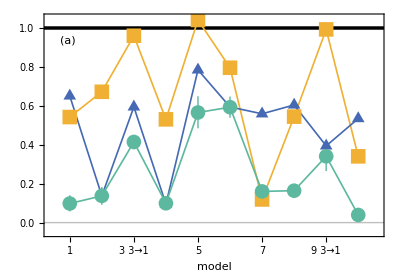
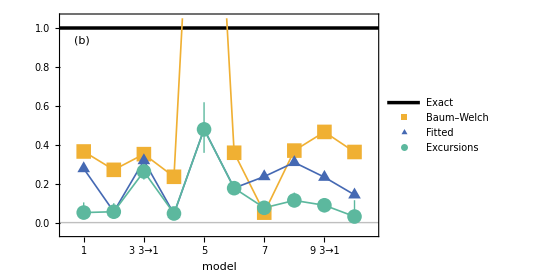
-Graphics- | -Graphics-

```mathematica
grid[{affBenchPlotN,sigBenchPlotN}, 1, {0.07, 0.88}, 24]
```

```mathematica
Export["benchmark-simulations.pdf",%]
```

benchmark-simulations.pdf